```mathematica
Quit
```

```mathematica
q = 1;
M = 1;
```

## Prelims

### Definitions

```mathematica
WP = 75;
```

```mathematica
WPI = 275;
```

```mathematica
lgQ[l_,x_]:= (
SetPrecision[LegendreQ[l,0,3,SetPrecision[x, WP]],WP]
) 
dlgQ[l_,x_]:=(
SetPrecision[1/(-1+SetPrecision[x, WP]^2)((-1-l) SetPrecision[x, WP] LegendreQ[l,0,3,SetPrecision[x, WP]]+(1+l) LegendreQ[1+l,0,3,SetPrecision[x, WP]]),WP]
)
```

### Interior Schwarzschild Setup

```mathematica
μ[Z_] =  ((√(8Z-10))/(3 √(Z-1)-√(Z+1)))^-1;
Htanχz[ζ_,Z_] =  1/μ[Z] √((Z+1)^3/(2(ζ+1)^2))(1-√(1-2(ζ+1)^2/(Z+1)^3));
sinχz[ζ_,Z_] = (2Htanχz[ζ,Z])/(1+Htanχz[ζ,Z]^2);
cosχz[ζ_,Z_] = (1-Htanχz[ζ,Z]^2)/(1+Htanχz[ζ,Z]^2);
dχdz[ζ_, Z_] = (2 D[Htanχz[ζ,Z],ζ])/(1+Htanχz[ζ,Z]^2)//FullSimplify; 
sinxby2[ζ_,Z_] = √((1-cosχz[ζ,Z])/2);
```

```mathematica
κ[l,M]ν[l,M]
```

κ[l,1] ν[l,1]

#### Scalar Field Solution and Prelims: Charge in the exterior

```mathematica
SΦtmp[l_,ζ_,Z_] =  ((M^2(Z+1)^4)/(4Z-5))^(-1/2)(LegendreP[-1/2 ,-1/2 (1+2 l),cosχz[ζ,Z]]/(√sinχz[ζ,Z](1/2(3 √((Z-1)/(Z+1))-1) (1+Htanχz[ζ,Z]^2)/(1+μ[Z]^2 Htanχz[ζ,Z]^2)))) ;
ηZ[l_,Z_] = (ζ+1)/SΦtmp[l,ζ,Z] D[SΦtmp[l,ζ,Z],ζ]/.ζ-> Z;
SLZ[l_,Z_] := SetPrecision[ ((Z+1)(D[LegendreP[l,ζ],ζ]/.ζ-> Z)-(ηZ[l,Z])LegendreP[l,Z])/((Z+1)(dlgQ[l,Z])-(ηZ[l,Z])lgQ[l,Z]),WP];
```

#### Scalar Field Solution and Prelims: Charge in the interior

```mathematica
ηQ[l_,ζ_] = (ζ+1)/lgQ[l,ζ] dlgQ[l,ζ] ;
```

```mathematica
Π[l_,ζ_, Z_] =2((M^2(Z+1)^4)/(4Z-5))^(-1/2)LegendreP[-1/2, -l-1/2, cosχz[ζ,Z]]/((-3 √((-1+Z)/(1+Z))+√(1-(2 (1+ζ)^2)/(1+Z)^3))√sinχz[ζ,Z]);
Θ[l_,ζ_, Z_] =2((M^2(Z+1)^4)/(4Z-5))^(-1/2)LegendreP[-1/2, l+1/2, cosχz[ζ,Z]]/((-3 √((-1+Z)/(1+Z))+√(1-(2 (1+ζ)^2)/(1+Z)^3))√sinχz[ζ,Z]);
```

```mathematica
Wr[l_, ζ_, Z_] = (-1)^(l+1)/sinχz[ζ,Z]^2 2/π (4((M^2(Z+1)^4)/(4Z-5))^-1)/((-3 √((-1+Z)/(1+Z))+√(1-(2 (1+ζ)^2)/(1+Z)^3))^2)dχdz[ζ,Z];
Str[l_,Z_] = ((Z+1) (D[Θ[l,ζ,Z],ζ])-ηQ[l,Z]Θ[l,ζ,Z])/((Z+1) (D[Π[l,ζ,Z],ζ])-ηQ[l,Z]Π[l,ζ,Z])/.ζ->Z;
```

#### Electric Field Solution and Prelims: Charge in the exterior

```mathematica
EMΦtmp[ζ_,Z_,l_, M_:1] = LegendreP[1/2 ,-1/2 (1+2 l),cosχz[ζ,Z]]/(√sinχz[ζ,Z]) ;
EMη[ζ_,Z_,l_] = (ζ+1)/EMΦtmp[ζ,Z,l] D[EMΦtmp[ζ,Z,l],ζ];
EMηZ[l_,Z_] = EMη[ζ,Z,l]/.ζ-> Z(*Assuming[{Z>5/4, l>0}, EMη[Z,Z,l]/.ζ-> Z]*);
κ[l_, M_:1] = (2^l l!(l-1)!M^(l-1))/((2l)!);
ν[l_, M_:1] = - ((2l+1)!)/(2^l l!(l+1)!M^(l+2));
EMp[l_,ζ_, M_:1] = κ[l, M](ζ-1)(D[LegendreP[k,x], x]/.{x-> ζ, k-> l});
EMq[l_,ζ_, M_:1] = ν[l ,M](ζ-1)(dlgQ[l,ζ]);
EMSlz[l_,Z_] =((x+1)(D[EMp[l,x], x]) - EMηZ[l,x]EMp[l,x])/((x+1)(D[EMq[l,x], x]) - EMηZ[l,x]EMq[l,x])/.{x-> Z};
```

```mathematica
-(√(z^2-1))/(z+1)^2-1/(z+1)^2 Integrate[(z^2-1)D[(z-1)D[LegendreQ[0,0,3,z],z],z],z]//FullSimplify
```

-(z+√(-1+z^2)-2 Log[1+z])/(1+z)^2

```mathematica
D[(z-√(z^2-1))/(z+1)^2,z]//FullSimplify
```

((-z+√(-1+z^2)) (1+z+2 √(-1+z^2)))/((1+z)^3 √(-1+z^2))

```mathematica
D[(z+1)^2(z-1)D[LegendreQ[0,0,3,z],z],z]//FullSimplify
```

-1

```mathematica
D[LegendreQ[0,0,3,z],z]//FullSimplify
```

1/(1-z^2)

#### Electric Field Solution and Prelims: Charge in the interior

```mathematica
EMq[l_,ζ_, M_:1] = SetPrecision[ν[l ,M](ζ-1)(dlgQ[k,x]/.{x-> ζ, k-> l}), WPI];
EMηQ[l_,ζ_] = (x+1)/EMq[l,x] D[EMq[k,x],x]/.{x-> ζ, k-> l} ; 
EMΠ[l_,ζ_, Z_] =SetPrecision[LegendreP[1/2, -l-1/2, cosχz[ζ, Z]]/(√sinχz[ζ,Z])/.M-> 1, WPI];

EMSΠ[l_,χ_] =LegendreP[1/2, -l-1/2,Cos[χ]]/(√Sin[χ]);
EMΘ[l_,ζ_, Z_] =SetPrecision[LegendreP[1/2, l+1/2, cosχz[ζ, Z]]/(√sinχz[ζ,Z])/.M-> 1, WPI]; 
EMWz[l_, ζ_, Z_] =SetPrecision[(-1)^(l+1)/sinχz[ζ,Z]^2 2/π dχdz[ζ,Z]/.M-> 1, WPI];
EMStr[l_,Z_] = SetPrecision[((Z+1) (D[EMΘ[l,ζ,Z],ζ])-EMηQ[l,Z]EMΘ[l,Z,Z])/((Z+1) (D[EMΠ[l,ζ,Z],ζ])-EMηQ[l,Z]EMΠ[l,Z,Z])/.ζ->Z, WPI];
```

### Scalar Charge in the Exterior: Definitions etc

#### Regularisation Parameters

```mathematica
f[r_] = 1-2 M/r;
```

```mathematica
g[r_] = 1/2 Log[f[r]];
```

```mathematica
SBr[r_,M_] = -1/(2 r^2)(1+r g'[r]);
SDr[r_,M_] = -1/(16 r^2)((1+r g'[r])-(1+ r g'[r]+3 r^2 g'[r]^2+r^3 g'[r]^3-6 r^2 g''[r]-2 r^3 g'''[r])f[r] + (1+4r g'[r]+3 r^2 g''[r])r f'[r] + (1+r g'[r])r^2 f''[r]);
```

```mathematica
NumSBz[ξ_] = SetPrecision[q^2 SBr[r,M]/.{r-> M(ξ+1)} , WP];
```

```mathematica
NumSDz[ξ_] = SetPrecision[q^2 SDr[r,M]/.{r-> M(ξ+1)}, WP];
```

#### Regularised Force

```mathematica
(*Forces are with the index downstairs i.e. Subscript[F, r]*)
```

```mathematica
BareExtModes[l_, ξ_, Z_] = 1/2(q/M)^2(2l+1)((ξ-1)/(ξ+1) )^(1/2) (LegendreP[l,ξ]dlgQ[l,ξ]+(D[LegendreP[l,x], x]/.x-> ξ)lgQ[l,ξ]-2SLZ[l,Z]lgQ[l,ξ]dlgQ[l,ξ])  ;
```

```mathematica
SSRegFB[l_, ξ_, Z_] = SetPrecision[BareExtModes[l, ξ, Z] - NumSBz[ξ], WP];
```

```mathematica
SSRegFD[l_, ξ_, Z_] = SetPrecision[BareExtModes[l, ξ, Z] - NumSBz[ξ]-NumSDz[ξ]/((l-1/2)(l+3/2)), WP];
```

```mathematica
Scadiff[l_,ξ_,Z_]= -(q/M)^2((ξ-1)/(ξ+1))^(1/2)(2l+1)SLZ[l,Z]lgQ[l,ξ]dlgQ[l,ξ];
```

```mathematica
ExtStarDirReg[Z_, ξ_,lm_:1,prec_:WP] :=  Module[{ZN,ξN,pcN,lmax,terms,modes,coeff,partsum, tail, force},
ZN = SetPrecision[Z, prec];
ξN = SetPrecision[ξ, prec];
pcN = SetPrecision[0.8, prec];
lmax = If[lm==1,If[ξ-Z <= 0.1,(2π (ZN+1))/(ξN-ZN), Max[200,lm]],lm];     
terms = Round[pcN*lmax];
(*Direct method*)
modes = Table[{l,SetPrecision[SSRegFD[l,ξN, ZN],prec]}, {l,Range[0,lmax]}];
coeff = Fit[modes[[terms;;]], {(l+1/2)^-4}, l][[1]];
partsum = Sum[Indexed[modes[[All,2]], m], {m,1,Length[modes]}];
tail = coeff*Sum[1/(l+1/2)^4, {l,Length[modes]+1, Infinity}]; 
force = SetPrecision[(partsum + tail), prec];
{force,partsum,lmax,coeff}
]
```

```mathematica
ExtStarDiffReg[Z_, ξ_,lm_:1,prec_:WP] :=  Module[{ZN, ξN, lmax, modes, terms, coeff, partsum, tail, force,l, pcN, DC, diffmodes, diffpartsum, difftail, diffforce,approxforce,approxsum},
ZN = SetPrecision[Z, prec];
ξN = SetPrecision[ξ, prec];
pcN = SetPrecision[0.8, prec];
lmax = If[lm==1,If[ξ-Z <= 0.1,(2π (ZN+1))/(ξN-ZN), 200],lm];     
terms = Round[pcN*lmax];
(*Difference Method*)
diffmodes = Table[{l,SetPrecision[Scadiff[l,ξN,ZN],prec]}, {l,Range[0,lmax]}];
DC = Fit[diffmodes[[terms;;]], {ⅇ^(-Log[(ξN+√(ξN^2-1))/(ZN+√(ZN^2-1))](2l+1))},l][[1]]; 
diffpartsum = Sum[Indexed[diffmodes[[All,2]], m], {m,1,Length[diffmodes]}];
difftail = DC*Sum[ⅇ^(-Log[(ξN+√(ξN^2-1))/(ZN+√(ZN^2-1))](2l+1)), {l,Length[diffmodes]+1, Infinity}];   
diffforce = SetPrecision[(diffpartsum + difftail), prec];
approxsum = SetPrecision[1/(4 (1+ZN) √(ξN-1) (ξN+1)^(3/2))Log[Coth[1/2 Log[(ξN+√(ξN^2-1))/(ZN+√(ZN^2-1))]]],prec]; 
{diffforce,diffpartsum,approxsum, lmax}
]
```

### EM Charge in the Exterior: Definitions etc

#### Regularisation Parameters

```mathematica
f[r_] = 1-2 M/r;
```

```mathematica
g[r_] = 1/2 Log[f[r]];
```

```mathematica
EMBr[r_,M_:1] = -1/(2 r^2)(1-r g'[r]);
EMDr[r_, M_:1] = -1/(16 r^2)((1-r g'[r])-(1- r g'[r]+3 r^2 g'[r]^2-r^3 g'[r]^3+6 r^2 g''[r]+2 r^3 g'''[r])f[r] + (1-4r g'[r]-3 r^2 g''[r])r f'[r] + (1-r g'[r])r^2 f''[r]);
```

```mathematica
BHexres[r_,M_:1,e_:1] = SetPrecision[(e^2 M)/r^3(1-2 M/r)^(-1/2),WP];
```

#### Regularisation

```mathematica
BHf[ξ_]= SetPrecision[(e^2 M)/r^3(1-2 M/r)^(-1/2)/.r-> M(ξ+1)/.e-> 1/.M-> 1//FullSimplify, WP];
```

```mathematica
EMBareExtModes[ln_,ξ_,Z_, q_:1, M_:1] = Module[{ξn, Zn, tmp, l},
tmp = -(1/2 q^2/(√((y-1)/(y+1)))((D[EMp[l,y], y]EMq[l,y])+(D[EMq[l,y],y]EMp[l,y])-2 EMSlz[l,Z]EMq[l,y]D[EMq[l,y],y]))/.y-> ξ ;
tmp/.l-> ln];
```

```mathematica
EMF0[ξ_, Z_, q_:1, M_:1] = 1/2(q/(M(ξ+1)))^2 √((ξ+1)/(ξ-1))/.{q-> 1, M-> 1};
```

```mathematica
EMBz[ξ_] = EMBr[r,M]/.r-> M(ξ+1)/.M-> 1//FullSimplify;
EMDz[ξ_] = EMDr[r,M]/.r-> M(ξ+1)/.M-> 1//FullSimplify;
```

```mathematica
EMSFdiff[l_,ξ_, Z_, q_:1, M_:1] = -(q/M)^2((ξ-1)/(ξ+1))^(1/2)(2l+1)((l(l+1)LegendreP[l,Z]-(1+EMηZ[l,Z])(Z-1)(D[LegendreP[k,x],x]/.{x-> Z, k-> l}))/(l(l+1)lgQ[l,Z]-(1+EMηZ[l,Z])(Z-1)(dlgQ[k,x]/.{x-> Z, k-> l})))(lgQ[l,ξ]-(ξ-1)/(l(l+1))dlgQ[l,ξ])dlgQ[l,ξ];
```

```mathematica
EMextapprox[l_,Z_,δ_]=(3  (Z+√(-1+Z^2))^(2 l+1) (Z+δ+√(-1+(Z+δ)^2))^(-2 l-1))/(4 (l+1/2)  (1+Z) √(-1+Z+δ) (1+Z+δ)^(3/2));
```

```mathematica
EMExtStarDirReg[Z_, ξ_,lm_:1,prec_:WP] :=  Module[{ZN,ξN,pcN,lmax,terms,modes,coeff,partsum, tail, force,RegEMmodes},
ZN = SetPrecision[Z, prec];
ξN = SetPrecision[ξ, prec];
pcN = SetPrecision[0.8, prec];
lmax = If[lm==1,If[ξ-Z <= 0.1,(2π (ZN+1))/(ξN-ZN), Max[200,lm]],lm];     
terms = Round[pcN*(lmax)];
(*Direct regularisation method*)
RegEMmodes = Table[{l,SetPrecision[EMBareExtModes[l,ξN, ZN]+EMBz[ξN]+EMDz[ξN]/((l-1/2)(l+3/2)), prec]}, {l,1,lmax}];  
PrependTo[RegEMmodes, {0,SetPrecision[EMF0[ξN, ZN]+EMBz[ξN]-4 EMDz[ξN]/3, prec]}]; 
coeff = Fit[RegEMmodes[[terms;;]], {(l+1/2)^-4}, l][[1]];
partsum = Sum[Indexed[RegEMmodes[[All,2]], m], {m,1,Length[RegEMmodes]}];
tail = coeff*Sum[1/(l+1/2)^4, {l,Length[RegEMmodes]+1, Infinity}];
force = SetPrecision[partsum + tail, prec];
{force,partsum,lmax}
]
```

```mathematica
EMExtStarDiffReg[Z_, ξ_,lm_:1,prec_:WP] :=  Module[{ZN, ξN, lmax, modes, terms, coeff, partsum, tail, force,l, pcN, DC, diffmodes, diffpartsum, difftail, diffforce,approxforce,approxsum,ΩEM,bhforce},
ZN = SetPrecision[Z, prec];
ξN = SetPrecision[ξ, prec];
pcN = SetPrecision[0.8, prec];
lmax = If[lm==1,If[ξ-Z <= 0.1,(2π (ZN+1))/(ξN-ZN), 200],lm];     
terms = Round[pcN*lmax];
(*Difference Method*)
ΩEM = Log[(ξN+√(ξN^2-1))/(ZN + √(ZN^2-1))]; 
diffmodes = Table[{l,SetPrecision[EMSFdiff[l,ξN,ZN],prec]}, {l,1,lmax}];
diffpartsum = Sum[Indexed[diffmodes[[All,2]], m], {m,1,Length[diffmodes]}];
DC = Fit[diffmodes[[terms;;]], {ⅇ^(-ΩEM(2l+1))},l][[1]]; 
difftail = DC*Sum[ⅇ^(-ΩEM(2l+1)), {l,Length[diffmodes]+1, Infinity}];
diffforce = SetPrecision[diffpartsum+difftail, prec]; 
(*differror  = SetPrecision[EMSFdiff[lmax+1,ξN,ZN],prec];*)
bhforce = SetPrecision[(1/(ξN+1))^3((ξN-1)/(ξN+1))^(-1/2),prec];
{diffforce,diffpartsum,lmax,bhforce}
]
```

```mathematica
EMSRS[Z_,pc_:0.80,q_:1, M_:1,prec_:WP] :=Module[{ ϵvals, results, termsdata, taildata, nsumdata, forcedata, dfdata, ZN , ξvals, modesdata, diffmodesdata}, 
ϵvals = Subdivide[SetPrecision[0.25, prec],SetPrecision[0.01, prec], 15];
(*Print[zvals];*)
ZN = SetPrecision[Z, prec];
ξvals = ZN+ϵvals;
results = Table[Print[StringForm["For ξ value `1`, generating data", ξ]];EMStarSuperSum[ Z,ξ,pc], {ξ,ξvals}];
(*taildata = Table[{zvals[[i]],results[[i,2]]}, {i,1,Length[zvals]}];
nsumdata = Table[{zvals[[i]],results[[i,3]]}, {i,1,Length[zvals]}];*)
forcedata = Table[{ϵvals[[i]],results[[i,1]]}, {i,1,Length[ξvals]}];
modesdata = Table[{ξvals[[i]],results[[i,3]]}, {i,1,Length[ξvals]}];
dfdata = Table[{ϵvals[[i]],results[[i,2]]}, {i,1,Length[ξvals]}];
diffmodesdata = Table[{ξvals[[i]],results[[i,4]]}, {i,1,Length[ξvals]}];
{forcedata, dfdata,modesdata, diffmodesdata, ξvals}
]
```

### Scalar Charge in the Interior: Definitions etc

#### Parameters

```mathematica
Afunc[r_,R_] = 1/4 (-3 √(1-(2M)/R)+√(1-(2M r^2)/R^3))^2;
Bfunc[r_,R_] =1-(2M r^2)/R^3;
```

```mathematica
rgψ[r_, R_] = 1/2 Log[Afunc[r,R]];
```

```mathematica
IntB[r_,R_] = - 1/(2 x^2)(1 + x D[rgψ[x,R], x] )/.x-> r;
```

```mathematica
intBz[ξ_, Z_] = IntB[r,R]/.{r-> M(ξ+1), R-> M(Z+1)}//FullSimplify;
```

#### Regularised Force

```mathematica
(*Forces are with the index downstairs i.e. Subscript[F, r]*)
```

```mathematica
BareIntModes[l_, ξ_, Z_] =  -1/2(q/(ξ+1))^2((2l+1)/(√(1-(2 (1+ξ)^2)/(1+Z)^3)  Wr[l,ξ,Z]))(Π[l,ξ,Z](D[Θ[l,r,Z],r]/.{r-> ξ})+Θ[l,ξ,Z](D[Π[l,r,Z],r]/.{r-> ξ}) -2 Str[l,Z](D[Π[l,r,Z],r]/.{r-> ξ})Π[l,ξ,Z]);
```

```mathematica
zRegForce[l_,ξ_,Z_] = SetPrecision[BareIntModes[l,ξ,Z]-intBz[ξ, Z],WPI];
```

```mathematica
intdiff[l_,ξ_,Z_]= (q/(ξ+1))^2((2l+1)/(√(1-(2 (1+ξ)^2)/(1+Z)^3)  Wr[l,ξ,Z]))( Str[l,Z](D[Π[l,r,Z],r]/.{r-> ξ})Π[l,ξ,Z]);
```

```mathematica
IntStarDirReg[Z_,ξ_,lm_:1, pc_:0.80,prec_:WPI] :=Module[{l,ZN, ξN,lmax,  terms ,modes, force, pcN, coeff, partsum, tail, diffmodes, diffcoeff, diffpartsum, difftail, diffforce, terms2,tailerror}, 
ZN = SetPrecision[Z ,prec];
ξN = SetPrecision[ξ,prec];
pcN = SetPrecision[pc, prec];
lmax = If[lm==1,If[Z-ξ <= 0.1, If[Z == 2 && ξ == 1.99,1425, Max[Round[(2π (ZN+1))/(ZN-ξN)],lm]], 500],lm];
terms = Round[pcN*(lmax+1)];   
modes = Table[{l,SetPrecision[zRegForce[l, ξN, ZN],prec]},{l,0,lmax}];
coeff = Fit[modes[[terms;;]], {(l+1/2)^-2}, l][[1]];
partsum = Sum[Indexed[modes[[All,2]], m], {m,1,lmax}];
tail = coeff*Sum[1/(l+1/2)^2, {l,lmax+1, Infinity}];
force = SetPrecision[(partsum + tail), WP];
tailerror=SetPrecision[Abs[tail]*0.001,WP];
{force, partsum, lmax, tailerror}
]
```

```mathematica
IntStarDiffReg[Z_,ξ_,lm_:1, pc_:0.80,prec_:WPI] :=Module[{difftailerror,l,ZN, ξN,lmax,  terms ,modes, force, pcN, coeff, partsum, tail, diffmodes, diffcoeff, diffpartsum, difftail, diffforce, terms2}, 
ZN = SetPrecision[Z ,prec];
ξN = SetPrecision[ξ,prec];
pcN = SetPrecision[pc, prec];
lmax = If[lm==1,If[Z-ξ <= 1,  Round[(2π (ZN+1))/(ZN-ξN)], 25],lm];
terms2 = Round[pcN*(lmax)];   
diffmodes = Table[{l,SetPrecision[intdiff[l, ξN, ZN],prec]},{l,0,lmax}];
diffcoeff = Fit[diffmodes[[terms2;;]], {ⅇ^(-(l+1/2))}, l][[1]];
diffpartsum = Sum[Indexed[diffmodes[[All,2]], m], {m,1,terms2}];
difftail = diffcoeff*Sum[ⅇ^(-(l+1/2)), {l,terms2+1, Infinity}];
diffforce = SetPrecision[(diffpartsum + difftail), WP];
difftailerror=SetPrecision[Abs[difftail]*0.001,WP];
{diffforce, diffpartsum, lmax,difftailerror}
]
```

### EM Charge in the Interior: Definitions etc

#### Parameters

```mathematica
Afunc[r_,R_] = 1/4 (-3 √(1-(2M)/R)+√(1-(2M r^2)/R^3))^2;
Bfunc[r_,R_] =1-(2M r^2)/R^3;
```

```mathematica
rgψ[r_, R_] = 1/2 Log[Afunc[r,R]];
```

```mathematica
EMIntB[r_,R_,M_] = SetPrecision[- 1/(2 x^2)(1 - x D[rgψ[x,R], x] )/.x-> r, WPI];
EMIntD[r_, R_,M_] = -1/(16 x^2)((1 - x D[rgψ[x,R], x] ) - (1 - x D[rgψ[x,R], x] + 3 x^2 D[rgψ[x,R], x]^2 - x^3 D[rgψ[x,R], x]^3 + 6 x^2 D[rgψ[x,R], {x,2}]+ 2 x^3 D[rgψ[x,R], {x,3}])Bfunc[x,R] + (1 - 4 x D[rgψ[x,R], x] - 3 x^2 D[rgψ[x,R], {x,2}])x D[Bfunc[x,R],x] + (1 - x D[rgψ[x,R], x] ) x^2 D[Bfunc[x,R], {x,2}])/.x-> r;
```

```mathematica
EMintBz[ξ_, Z_, M_:1, q_:1] = SetPrecision[EMIntB[r,R,1]/.{r-> (ξ+1), R-> Z+1, M-> 1}//FullSimplify, WPI];
EMintDz[ξ_, Z_, M_:1, q_:1] = SetPrecision[EMIntD[r,R,1]/.{r-> (ξ+1), R-> Z+1, M-> 1}//FullSimplify, WPI];
```

#### Regularised Force

```mathematica
(*Forces are with the index downstairs i.e. Subscript[F, r]*)
```

```mathematica
EMBareIntModes[l_, ξ_, Z_, q_:1, M_:1] =  Module[ {ξN, ZN, fr, x, Y, k},
ξN = SetPrecision[ξ,WPI];
ZN = SetPrecision[Z,WPI];
fr = SetPrecision[1/2(q/(M(x+1)))^2((2k+1)/(√(1-(2 (1+x)^2)/(1+Y)^3)  EMWz[k,x,Y]))(EMΘ[k,x,Y](D[EMΠ[k,r,Y],r]/.{r-> x})+EMΠ[k,x,Y](D[EMΘ[k,r,Y],r]/.{r-> x}) -2 EMStr[k,Y](D[EMΠ[k,r,Y],r]/.{r-> x})EMΠ[k,x,Y]), WPI];
fr/.{x-> ξN, Y-> ZN, k-> l}
];
EMintdiff[l_, ξ_, Z_, q_:1, M_:1] =  Module[ {ξN, ZN, fr, x, Y, k},
ξN = SetPrecision[ξ,WPI];
ZN = SetPrecision[Z,WPI];
fr = SetPrecision[-(q/(M(x+1)))^2((2k+1)/(√(1-(2 (1+x)^2)/(1+Y)^3)  EMWz[k,x,Y]))(EMStr[k,Y](D[EMΠ[k,r,Y],r]/.{r-> x})EMΠ[k,x,Y]), WPI];
fr/.{x-> ξN, Y-> ZN, k-> l}
];
```

```mathematica
EMzeroint[ξ_, Z_, q_:1, M_:1] =1/2 (q/(M(ξ+1)))^2 1/(√(1-(2 (1+ξ)^2)/(1+Z)^3));
```

```mathematica
EMIntStarDirReg[Z_,ξ_,lm_:1,pc_:0.80, q_:1, M_:1,prec_:WP] :=Module[{tailerror,l,ZN, ξN,tst, lmax, terms ,modes, force, pcN, coeff, partsum, tail, diffmodes, diffcoeff, diffpartsum, difftail, diffforce}, 
ZN = SetPrecision[Z ,prec];
ξN = SetPrecision[ξ,prec];
pcN = SetPrecision[pc, prec];
lmax = If[lm==1,If[Z-ξ <= 1, If[Z == 2 && ξ == 1.99,1467, Round[(2π (ZN+1))/(ZN-ξN)]], 750],lm];   
modes = Table[{l, SetPrecision[EMBareIntModes[l,ξN, ZN], prec] +SetPrecision[EMintBz[ξN, ZN],prec]+SetPrecision[EMintDz[ξN, ZN]/((l-1/2)(l+3/2)),prec]}, {l,1,lmax}];
PrependTo[modes, {0,SetPrecision[EMzeroint[ξN, ZN]+EMintBz[ξN, ZN]-4/3 EMintDz[ξN, ZN],prec]}];
(*Print["Finished data gen"];*)
(*terms = Round[pcN*Length[modes]];*)
coeff = SetPrecision[Fit[modes, {(l+1/2)^-4}, l],prec][[1]];
partsum = Sum[Indexed[modes[[All,2]], m], {m,1,Length[modes]}];
tail = coeff*Sum[SetPrecision[1/(l+1/2)^4,prec], {l,Length[modes]+1, Infinity}];
force = SetPrecision[(partsum + tail), WP];
tailerror = SetPrecision[Abs[tail*0.001], WP];
{force, partsum, lmax,tailerror}
]
```

```mathematica
EMIntStarDiffReg[Z_,ξ_, pc_:0.80, q_:1, M_:1,prec_:WPI] :=Module[{l,ZN, ξN,lmax,  terms ,pcN, EMintdiffforce, EMintdiffmodes, EMintdiffcoeff, EMintdiffpartsum, EMintdifftail,ΩEMint,approxEMforce}, 
ZN = SetPrecision[Z ,prec];
ξN = SetPrecision[ξ,prec];
pcN = SetPrecision[pc, prec];
lmax = If[Z-ξ <= 1, Round[(2π (ZN+1))/(ZN-ξN)], 25];   
(*Print@lmax;*)
(*Print@Round[(2π (ZN+1))/(ZN-ξN)];*)
EMintdiffmodes = Table[{l, SetPrecision[EMintdiff[l,ξN, ZN], prec]},{l,1,lmax}];
PrependTo[EMintdiffmodes, {0,0}];
EMintdiffcoeff = SetPrecision[Fit[EMintdiffmodes, {ⅇ^(-(l+1/2))}, l],prec][[1]];
EMintdiffpartsum = Sum[Indexed[EMintdiffmodes[[All,2]], m], {m,1,Length[EMintdiffmodes]}];
EMintdifftail = SetPrecision[EMintdiffcoeff*Sum[ⅇ^(-(l+1/2)), {l,Length[EMintdiffmodes]+1, Infinity}], prec];
EMintdiffforce = SetPrecision[(EMintdiffpartsum + EMintdifftail), WP];
{EMintdiffforce, EMintdiffpartsum, lmax}
]
```

## Numerical Evidence of Vanishing Mode-Sums

### Scalar Exterior

#### Regularisation Parameters

```mathematica
f[r_] = 1-2 M/r;
```

```mathematica
g[r_] = 1/2 Log[f[r]];
```

```mathematica
SBr[r_,M_] = -1/(2 r^2)(1+r g'[r]);
SDr[r_,M_] = -1/(16 r^2)((1+r g'[r])-(1+ r g'[r]+3 r^2 g'[r]^2+r^3 g'[r]^3-6 r^2 g''[r]-2 r^3 g'''[r])f[r] + (1+4r g'[r]+3 r^2 g''[r])r f'[r] + (1+r g'[r])r^2 f''[r]);
```

```mathematica
NumSBz[ξ_] = SetPrecision[q^2 SBr[r,M]/.{r-> M(ξ+1)} , WP];
```

```mathematica
NumSDz[ξ_] = SetPrecision[q^2 SDr[r,M]/.{r-> M(ξ+1)}, WP];
```

#### Sum

```mathematica
(*Forces are with the index downstairs i.e. Subscript[F, r]*)
```

```mathematica
BHRegModes[l_,ξ_,Z_] = SetPrecision[1/2(q/M)^2(2l+1)((ξ-1)/(ξ+1))^(1/2)(LegendreP[l,ξ]dlgQ[l,ξ]+(D[LegendreP[l,x],x]/.x-> ξ)lgQ[l,ξ])-NumSBz[ξ]-NumSDz[ξ]/((l-1/2)(l+3/2)),WP];
```

```mathematica
Assuming[m>0,SBr[r,m]/.{r-> m{ξ+1}}//FullSimplify]
```

{-(-1+m+m ξ)/(2 m^2 (1+ξ)^2 (-2+m+m ξ))}

```mathematica
ExtDirectSum[Z_, ξ_,lm_:1, prec_:WP, pc_:0.80] :=  Module[{ZN,ξN,pcN,lmax,terms,modes,coeff,partsum,tail,force,BHmodes,BHcoeff,BHpartsum,BHtail,BHforce},
ZN = SetPrecision[Z, prec];
ξN = SetPrecision[ξ, prec];
pcN = SetPrecision[pc, prec];
lmax = If[lm==1,If[ξ-Z <= 0.1,(2π (ZN+1))/(ξN-ZN), 200],lm];     
terms = Round[pcN*lmax];
(*BH SF*)
BHmodes = Table[{l,SetPrecision[BHRegModes[l,ξN, ZN],prec]}, {l,Range[0,lmax]}];
BHcoeff = Fit[BHmodes[[terms;;]], {(l+1/2)^-4}, l][[1]];
BHpartsum = Sum[Indexed[BHmodes[[All,2]], m], {m,1,Length[BHmodes]}];
BHtail = BHcoeff*Sum[1/(l+1/2)^4, {l,Length[BHmodes]+1, Infinity}]; 
BHforce = SetPrecision[(BHpartsum + BHtail), prec];
{BHpartsum,BHforce,lmax}
]
```

### Scalar Interior

#### Parameters

```mathematica
Afunc[r_,R_] = 1/4 (-3 √(1-(2M)/R)+√(1-(2M r^2)/R^3))^2;
Bfunc[r_,R_] =1-(2M r^2)/R^3;
```

```mathematica
rgψ[r_, R_] = 1/2 Log[Afunc[r,R]];
```

```mathematica
IntB[r_,R_] = - 1/(2 x^2)(1 + x D[rgψ[x,R], x] )/.x-> r;
```

```mathematica
intBz[ξ_, Z_] = IntB[r,R]/.{r-> M(ξ+1), R-> M(Z+1)}//FullSimplify;
```

#### Sum

```mathematica
intvpmodes[l_, ξ_, Z_] =  -1/2(q/(ξ+1))^2((2l+1)/(√(1-(2 (1+ξ)^2)/(1+Z)^3)  Wr[l,ξ,Z]))(Π[l,ξ,Z](D[Θ[l,r,Z],r]/.{r-> ξ})+Θ[l,ξ,Z](D[Π[l,r,Z],r]/.{r-> ξ}) );
```

```mathematica
IntDirectSum[Z_,ξ_,lm_:1, pc_:0.80,prec_:WPI] :=Module[{l,ZN, ξN,lmax,  terms ,modes, force, pcN, coeff, partsum, tail, diffmodes, diffcoeff, diffpartsum, difftail, diffforce, terms2,sum}, 
ZN = SetPrecision[Z ,prec];
ξN = SetPrecision[ξ,prec];
pcN = SetPrecision[pc, prec];
lmax = If[lm==1,If[Z-ξ <= 0.1, If[Z == 2 && ξ == 1.99,1425, Round[(2π (ZN+1))/(ZN-ξN)]], 500],lm];
terms = Round[pcN*(lmax+1)];   
modes = Table[{l,SetPrecision[intvpmodes[l, ξN, ZN]-intBz[ξN,ZN],prec]},{l,0,lmax}];
coeff = Fit[modes[[terms;;]], {(l+1/2)^-2}, l][[1]];
partsum = Sum[Indexed[modes[[All,2]], m], {m,1,terms}];
tail = coeff*Sum[1/(l+1/2)^2, {l,terms+1, Infinity}];
sum = SetPrecision[(partsum + tail), WP];
{partsum,sum,lmax}
]
```

### EM Interior

#### Parameters

```mathematica
Afunc[r_,R_] = 1/4 (-3 √(1-(2M)/R)+√(1-(2M r^2)/R^3))^2;
Bfunc[r_,R_] =1-(2M r^2)/R^3;
```

```mathematica
rgψ[r_, R_] = 1/2 Log[Afunc[r,R]];
```

```mathematica
EMIntB[r_,R_,M_] = SetPrecision[- 1/(2 x^2)(1 - x D[rgψ[x,R], x] )/.x-> r, WPI];
EMIntD[r_, R_,M_] = -1/(16 x^2)((1 - x D[rgψ[x,R], x] ) - (1 - x D[rgψ[x,R], x] + 3 x^2 D[rgψ[x,R], x]^2 - x^3 D[rgψ[x,R], x]^3 + 6 x^2 D[rgψ[x,R], {x,2}]+ 2 x^3 D[rgψ[x,R], {x,3}])Bfunc[x,R] + (1 - 4 x D[rgψ[x,R], x] - 3 x^2 D[rgψ[x,R], {x,2}])x D[Bfunc[x,R],x] + (1 - x D[rgψ[x,R], x] ) x^2 D[Bfunc[x,R], {x,2}])/.x-> r;
```

```mathematica
EMintBz[ξ_, Z_, M_:1, q_:1] = SetPrecision[EMIntB[r,R,1]/.{r-> (ξ+1), R-> Z+1, M-> 1}//FullSimplify, WPI];
EMintDz[ξ_, Z_, M_:1, q_:1] = SetPrecision[EMIntD[r,R,1]/.{r-> (ξ+1), R-> Z+1, M-> 1}//FullSimplify, WPI];
```

#### Force

```mathematica
EMintvpmodes[l_, ξ_, Z_, q_:1, M_:1] =  Module[ {ξN, ZN, fr, x, Y, k},
ξN = SetPrecision[ξ,WPI];
ZN = SetPrecision[Z,WPI];
fr = SetPrecision[1/2(q/(M(x+1)))^2((2k+1)/(√(1-(2 (1+x)^2)/(1+Y)^3)  EMWz[k,x,Y]))(EMΘ[k,x,Y](D[EMΠ[k,r,Y],r]/.{r-> x})+EMΠ[k,x,Y](D[EMΘ[k,r,Y],r]/.{r-> x}) ), WPI];
fr/.{x-> ξN, Y-> ZN, k-> l}
];
```

```mathematica
EMIntDirectSum[Z_,ξ_,lm_:1,pc_:0.80, q_:1, M_:1,prec_:WP] :=Module[{l,ZN, ξN,tst, lmax, terms ,modes, force, pcN, coeff, partsum, tail, diffmodes, diffcoeff, diffpartsum, difftail, diffforce,sum}, 
ZN = SetPrecision[Z ,prec];
ξN = SetPrecision[ξ,prec];
pcN = SetPrecision[pc, prec];
lmax = If[lm==1,If[Z-ξ <= 1, If[Z == 2 && ξ == 1.99,1467, Round[(2π (ZN+1))/(ZN-ξN)]], 500],lm];   
modes = Table[{l, SetPrecision[EMintvpmodes[l,ξN, ZN], prec] +SetPrecision[EMintBz[ξN, ZN],prec]+SetPrecision[EMintDz[ξN, ZN]/((l-1/2)(l+3/2)),prec]}, {l,1,lmax}];
PrependTo[modes, {0,SetPrecision[EMintvpmodes[0,ξN, ZN]+EMintBz[ξN, ZN]-4/3 EMintDz[ξN, ZN],prec]}];
(*Print["Finished data gen"];*)
(*terms = Round[pcN*Length[modes]];*)
coeff = SetPrecision[Fit[modes, {(l+1/2)^-4}, l],prec][[1]];
partsum = Sum[Indexed[modes[[All,2]], m], {m,1,Length[modes]}];
tail = coeff*Sum[SetPrecision[1/(l+1/2)^4,prec], {l,Length[modes]+1, Infinity}];
sum = SetPrecision[(partsum + tail), WP];
{partsum,sum,lmax}
]
```

### Part-Sum Plot

```mathematica
R3= SetPrecision[3,WP];
intr3=SetPrecision[1.5,WP];
extr3=SetPrecision[4.5,WP];
lmvals = Range[250,1000,75]
```

{250,325,400,475,550,625,700,775,850,925,1000}

```mathematica
BHPSdata = Table[BHres=ExtDirectSum[R3-1,extr3-1,li];{BHres[[3]],BHres[[1]]}, {li,lmvals}];
```

```mathematica
StarScalarPSdata = Table[IntRes=IntDirectSum[R3-1,intr3-1,li];{IntRes[[3]],IntRes[[1]]}, {li,lmvals}];
```

```mathematica
StarEMPSdata = Table[EMIntRes=EMIntDirectSum[R3-1,intr3-1,li];{EMIntRes[[3]],EMIntRes[[1]]}, {li,lmvals}];
```

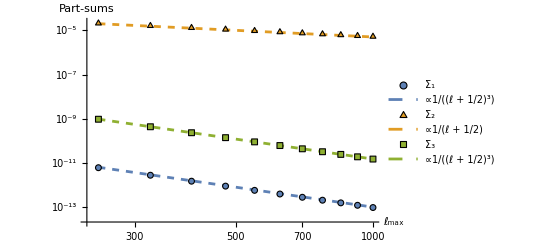

```mathematica
PartSumPlot=ListLogLogPlot[{BHPSdata,Table[{li,10^-4/(li+1/2)^3}, {li,lmvals}],Abs@StarScalarPSdata, Table[{li,(0.5*10^-2)/(li+1/2)}, {li,lmvals}],Abs@StarEMPSdata, Table[{li,(1.5*10^-2)/(li+1/2)^3}, {li,lmvals}]}, PlotStyle->{ColorData[97,"ColorList"][[1]],{ColorData[97,"ColorList"][[1]], Dashed},ColorData[97,"ColorList"][[2]],{ColorData[97,"ColorList"][[2]], Dashed},ColorData[97,"ColorList"][[3]],{ColorData[97,"ColorList"][[3]], Dashed}}, Joined->{False, True, False, True, False, True},AxesLabel->{Style["ℓ_max",14], Style["Part-sums", 14]}, PlotMarkers->{{Graphics[{EdgeForm[Black],Disk[]}],6},None,{Graphics[{EdgeForm[Black],Polygon[{{0,0},{1,0},{0.5,0.866}}]}],6},None,{Graphics[{EdgeForm[Black],Rectangle[]}],6},None},PlotLegends->{Style["Σ_1",14],Style["∝1/(ℓ + 1/2)^3",14],Style["Σ_2",14],Style["∝1/(ℓ + 1/2)",14],Style["Σ_3",14],Style["∝1/(ℓ + 1/2)^3",14]}]
```

```mathematica
Export["C:\\Users\\smp23ans\\Desktop\\Research\\Projects\\PhD\\Self Force Differences and Interior Schwarszchild\\Mathematica Code\\Part-Sum Plots.pdf", PartSumPlot]
```

C:\Users\smp23ans\Desktop\Research\Projects\PhD\Self Force Differences and Interior Schwarszchild\Mathematica Code\Part-Sum Plots.pdf

## Verifying Direct Regularisation

### Scalar Exterior

```mathematica
ξ0 = SetPrecision[15,WP];
Z0 = SetPrecision[10,WP];
lvals = 200;
```

```mathematica
ExtModes00= Table[{l,BareExtModes[l,ξ0, Z0]}, {l,lvals}];
```

```mathematica
ExtModes01 = Table[{l,BareExtModes[l,ξ0, Z0]-NumSBz[ξ0]}, {l,lvals}];
```

```mathematica
ExtModes02 = Table[{l,BareExtModes[l,ξ0, Z0]-NumSBz[ξ0]-NumSDz[ξ0]/((l-1/2)(l+3/2))}, {l,lvals}];
```

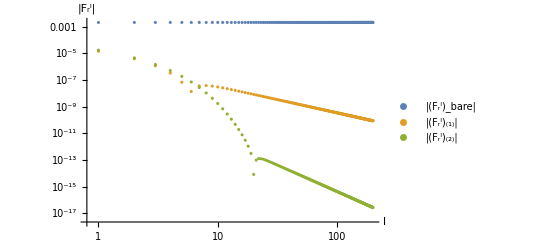

```mathematica
DirRegModes = ListLogLogPlot[{Abs[ExtModes00], Abs[ExtModes01],Abs[ExtModes02]}, PlotLegends->{"|(F_r^l)_bare|", "|(F_r^l)_(1)|", "|(F_r^l)_(2)|"}, AxesLabel->{"l", "|F_r^l|"}]
```

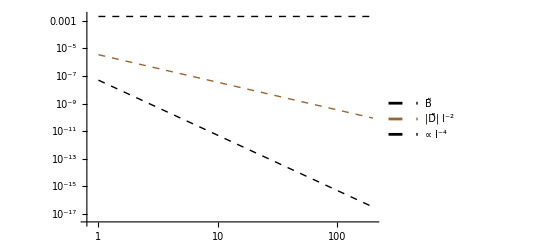

```mathematica
DirRegGuides = ListLogLogPlot[{Table[Abs[ NumSBz[ξ0]], {l,Range[1,lvals]}],Table[Abs[NumSDz[ξ0]] l^-2, {l,Range[1,lvals]}], Table[5*10^-8 l^-4, {l,Range[1,lvals]}]}, Joined -> True, PlotStyle->{{Black, Dashed, Thin}, {Brown,Dashed,  Thin}},PlotLegends->{ "B̃", "|D̃| l^-2", "∝ l^-4"}]
```

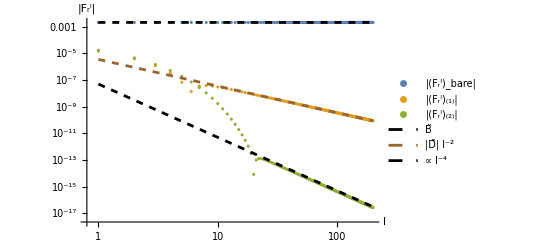

```mathematica
DirRegPlot= Show[DirRegModes, DirRegGuides]
```

### Scalar Interior

```mathematica
ξ2 = SetPrecision[5,WPI];
Z2 = SetPrecision[10,WPI];
lm4 = 200;
```

```mathematica
intmodes = Table[{l,SetPrecision[BareIntModes[l,ξ2,Z2],WPI]}, {l,0,lm4}];
```

```mathematica
intmodes01 = Table[{l,SetPrecision[zRegForce[l,ξ2,Z2],WPI]}, {l,0,lm4}];
```

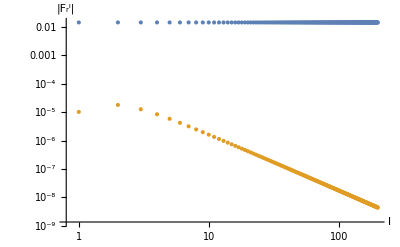

```mathematica
intmodesdat = ListLogLogPlot[{Abs[intmodes], Abs[intmodes01]},AxesLabel->{"l", "|F_r^l|"}]
```

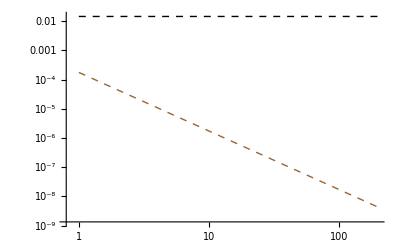

```mathematica
intguides = ListLogLogPlot[{Table[Abs[ intBz[ξ2, Z2]], {l,Range[1,lm4]}],Table[1.75*10^-4 l^-2, {l,Range[1,lm4]}]}, Joined -> True, PlotStyle->{{Black, Dashed, Thin}, {Brown,Dashed,  Thin}}]
```

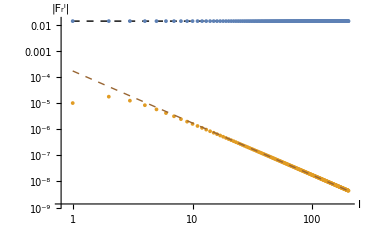

```mathematica
intregcurves = Show[intmodesdat, intguides]
```

```mathematica
ξ3 = SetPrecision[2,WPI];
Z3 = SetPrecision[3,WPI];
```

```mathematica
intdiffmodes= Table[{l,SetPrecision[intdiff[l,ξ3,Z3],WPI]}, {l,0,lm4}];
```

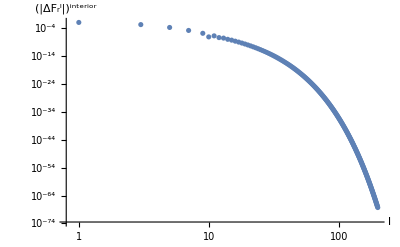

```mathematica
ListLogLogPlot[intdiffmodes, AxesLabel->{"l", "(|ΔF_r^l|)^interior"}]
```

### EM Exterior

```mathematica
bm = Table[SetPrecision[EMBareExtModes[l,ξ0,Z0],WP] ,{l,1,500}];
```

```mathematica
m1 =Table[SetPrecision[EMBareExtModes[l,ξ0,Z0]+EMBz[ξ0],WP] ,{l,1,250}];
```

```mathematica
m2 =  Table[SetPrecision[EMBareExtModes[l,ξ0,Z0]+EMBz[ξ0]+EMDz[ξ0]/((l-1/2)(l+3/2)) ,WP] ,{l,1,250}];
```

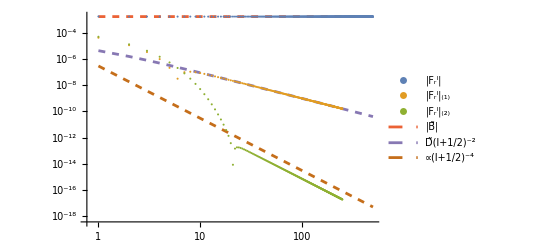

```mathematica
ListLogLogPlot[{Abs[bm], Abs[m1], Abs[m2], Table[Abs[EMBz[ξ0]], {l,1,500}],Table[EMDz[ξ0](l+1/2)^-2, {l,1,500}],Table[3*10^-7 l^-4, {l,1,500}]},Joined->{False, False, False, True, True, True},PlotStyle->{Thick, Thick, Thick, {Dashed},{Dashed},{Dashed}}, PlotLegends->{"|F_r^l|", "|F_r^l|_(1)", "|F_r^l|_(2)", "|B̃|", "D̃(l+1/2)^-2","∝(l+1/2)^-4"}]
```

### (*Needs a single run*) EM Interior

```mathematica
ξ2 = SetPrecision[5,WPI];
Z2 = SetPrecision[10,WPI];
lm4 = 200;
```

```mathematica
EMintmodes = Table[{l,SetPrecision[EMBareIntModes[l,ξ2,Z2],WPI]}, {l,0,lm4}];
```

```mathematica
EMintmodes01 = Table[{l,SetPrecision[EMBareIntModes[l,ξ2,Z2]+EMintBz[ξ2,Z2],WPI]}, {l,0,lm4}];
```

```mathematica
EMintmodes02 = Table[{l,SetPrecision[EMBareIntModes[l,ξ2,Z2]+EMintBz[ξ2,Z2]+EMintDz[ξ2,Z2]/((l-1/2)(l+3/2)),WPI]}, {l,0,lm4}];
```

```mathematica
ListLogLogPlot[{Abs[EMintmodes], Abs[EMintmodes01],Abs[EMintmodes02],Table[Abs[ EMintBz[ξ2,Z2]], {l,Range[1,lvals]}],Table[Abs[EMintDz[ξ2,Z2]] l^-2, {l,Range[1,lvals]}], Table[5*10^-8 l^-4, {l,Range[1,lvals]}]}, PlotLegends->{"|(F_r^l)_bare|", "|(F_r^l)_(1)|", "|(F_r^l)_(2)|"}, AxesLabel->{"l", "|F_r^l|"}]
```

```mathematica
ξ3 = SetPrecision[2,WPI];
Z3 = SetPrecision[3,WPI];
```

```mathematica
EMintdiffmodes= Table[{l,SetPrecision[EMintdiff[l,ξ3,Z3],WPI]}, {l,0,lm4}];
```

```mathematica
ListLogLogPlot[EMintdiffmodes, AxesLabel->{"l", "(|ΔF_r^l|)^interior"}]
```

-Graphics-

## Far Field Expansions: Analytics vs Numerics

### Scalar Far Field

We have an analytic expansion in the far field: F_r= q^2 M/(3 r^3)(S_0 + (2M)/r S_0 + (23 M^2)/(6 r^2)S_0 + (2 R^2)/(5 r^2)S_1+....)
with S_0= 1 - 8/5 M/R-67/105(M/R)^2-368/315(M/R)^3+.....  and 
S_1 = 1- 32/21 M/R + 158/315(M/R)^2 - 9472/7425(M/R)^3-298996/257985(M/R)^4+...
____________________________________________________________
Note that SLZ[l,Z] in the code is NOT the normalised structure factor. SLZ[0,Z] = 1/3 S_0

```mathematica
R0 = SetPrecision[50,WP];
rmm = SetPrecision[100,WP];
rmax02 = SetPrecision[3000,WP];
```

```mathematica
S0[R_] = 1-(2235496 M^5)/(675675 R^5)-(3589 M^4)/(1925 R^4)-(368 M^3)/(315 R^3)-(67 M^2)/(105 R^2)-(8 M)/(5 R);
S1[R_] = 1-(298996 M^4)/(257985 R^4)-(9472 M^3)/(7425 R^3)+(158 M^2)/(315 R^2)-(32 M)/(21 R);
SE[r_, R_, q_:1, M_:1] = q^2 M/(3 r^3)(S0[R] + (2M)/r S0[R] + (23 M^2)/(6 r^2)S0[R] + (2 R^2)/(5 r^2)S1[R]);
```

Order by Order Plot

```mathematica
forcedat = Table[{r0,SetPrecision[r0^3 ExtStarDirReg[R0-1, r0-1][[1]], WP]}, {r0,Range[rmm,rmax02, 100]}];
```

```mathematica
numforce01dat = Table[{r0,SetPrecision[r0^3 (ExtStarDirReg[R0-1, r0-1][[1]]-SLZ[0,R0-1]/r0^3) , WP]},{r0,Range[rmm,rmax02, 100]}];
```

```mathematica
numforce02dat = Table[{r0,SetPrecision[r0^3 (ExtStarDirReg[R0-1, r0-1][[1]]-SLZ[0,R0-1]/r0^3-2 SLZ[0,R0-1]/r0^4) , WP]},{r0,Range[rmm,rmax02, 100]}];
```

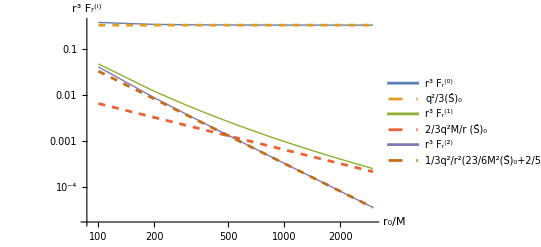

```mathematica
oboforces =ListLogLogPlot[{forcedat, Table[{r,SLZ[0,R0-1]},{r,forcedat[[All,1]]}],numforce01dat,Table[{r,2/r SLZ[0,R0-1]},{r,numforce01dat[[All,1]]}],numforce02dat,Table[{r,(23/6 SLZ[0,R0-1]+2/3 SLZ[1,R0-1])1/r^2},{r,numforce02dat[[All,1]]}]}, PlotLegends->{"r^3 F_r^(0)"," q^2/3(Ŝ)_0", "r^3 F_r^(1)",  "2/3q^2M/r (Ŝ)_0","r^3 F_r^(2)", "1/3q^2/r^2(23/6M^2(Ŝ)_0+2/5R^2 (Ŝ)_1)"}, PlotRange->All, Joined->True, PlotStyle->{Thick,Dashed, Thick, Dashed, {Thick},{ Dashed}}, AxesLabel->{"r_0/M", "r^3 F_r^(i)"}]
```

```mathematica
Export["C:\\Users\\smp23ans\\Desktop\\Research\\Projects\\PhD\\Self Force Differences and Interior Schwarszchild\\Mathematica Code\\Force vs Exp Plots\\orderbyorder.pdf", oboforces]
```

C:\Users\smp23ans\Desktop\Research\Projects\PhD\Self Force Differences and Interior Schwarszchild\Mathematica Code\Force vs Exp Plots\orderbyorder.pdf

### EM Far Field

We have an analytic expansion in the far field: F_r= -(2 q^2 M)/15 R^2/r^5(2 S_1^EM + (7M)/r S_1^EM +91/5(M^2 R^2)/r^2 S_1^EM(9 R^4)/(35 r^2)S_2^EM+....)
with S_1^EM= 1 - 8/7 M/R-61/105(M/R)^2-472/825(M/R)^3-392507/525525(M/R)^4-...  and S_2^EM= 1 - 184/45 M/R-10152/1925(M/R)^2-4496896/2627625(M/R)^3-566696/1299375(M/R)^4

```mathematica
R0 = SetPrecision[50,WP];
rmm = SetPrecision[100,WP];
rmax02 = SetPrecision[3000,WP];
```

```mathematica
EMS1[R_] = 1 - 8/7 M/R-61/105(M/R)^2-472/825(M/R)^3-392507/525525(M/R)^4/.M-> 1;
EMS2[R_] = 1 - 184/45 M/R-10152/1925(M/R)^2-4496896/2627625(M/R)^3-566696/1299375(M/R)^4/.M-> 1;
EMSE[r_, R_, q_:1, M_:1] = (2 q^2 M)/5 R^2/r^5(EMS1[R] + (7M)/r EMS1[R] +91/10 M^2/r^2 EMS1[R]+(9 R^2)/(14 r^2)EMS2[R]);
```

Order by Order Plot

```mathematica
EMforcedat = Table[{r0,SetPrecision[r0^5 EMExtStarDiffReg[R0-1, r0-1][[1]], WP]}, {r0,Range[rmm,rmax02, 100]}];
```

```mathematica
EMnumforce01dat = Table[{r0,SetPrecision[r0^5 (EMExtStarDiffReg[R0-1, r0-1][[1]]-2/5 R0^2/r0^5(ν[1]/κ[1] EMSlz[1,R0-1] 10/(3 R0^2))) , WP]},{r0,Range[rmm,rmax02, 100]}];
```

```mathematica
EMnumforce02dat = Table[{r0,SetPrecision[r0^5 (EMExtStarDiffReg[R0-1, r0-1][[1]]-2/5 R0^2/r0^5(ν[1]/κ[1] EMSlz[1,R0-1] 10/(3 R0^2))-7/5 R0^2/r0^6(ν[1]/κ[1] EMSlz[1,R0-1] 10/(3 R0^2))), WP]},{r0,Range[rmm,rmax02, 100]}];
```

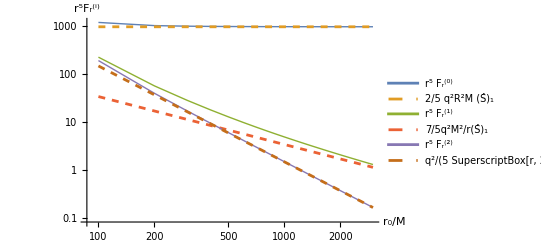

```mathematica
EMoboforces =ListLogLogPlot[{EMforcedat, Table[{r,2/5 R0^2(ν[1]/κ[1] EMSlz[1,R0-1] 10/(3 R0^2))},{r,EMforcedat[[All,1]]}],EMnumforce01dat, Table[{r,7/5 R0^2/r(ν[1]/κ[1] EMSlz[1,R0-1] 10/(3 R0^2))},{r,EMnumforce01dat[[All,1]]}],EMnumforce02dat,Table[{r,91/25 R0^2/r^2(ν[1]/κ[1] EMSlz[1,R0-1] 10/(3 R0^2))+9/35 R0^4/r^2(ν[2]/κ[2] EMSlz[2,R0-1] 14/(9 R0^4))},{r,EMnumforce02dat[[All,1]]}]}, PlotLegends->{"r^5 F_r^(0)","2/5 q^2R^2M (Ŝ)_1", "r^5 F_r^(1)",  "7/5q^2M^2/r(Ŝ)_1","r^5 F_r^(2)", "q^2/(5 SuperscriptBox[r, 2])MR^2 (91/5MR (Ŝ)_1+9/7R^2 (Ŝ)_2)"}, PlotRange->All, Joined->True, PlotStyle->{Thick,Dashed, Thick, Dashed, {Thick},{ Dashed}}, AxesLabel->{"r_0/M", "r^5F_r^(i)"}]
```

## Approaching the Boundary

### Scalar Exterior

#### Comparing asymptotics with exterior data

```mathematica
coeff[l_, Z_, δ_] =(q^2 (Z+√(-1+Z^2))^(2 l+1) (Z+δ+√(-1+(Z+δ)^2))^(-2 l-1))/(4 (l +1/2)M^2 (1+Z) √(-1+Z+δ) (1+Z+δ)^(3/2));
```

```mathematica
lm3 = 2000;
```

```mathematica
smodesext6 = Table[SetPrecision[SSRegFB[l,xp6,Z1], WP], {l,1,lm3}];
```

```mathematica
sdiffmodes6 = Table[SetPrecision[Scadiff[l,xp6,Z1],WP], {l,1,lm3}];
```

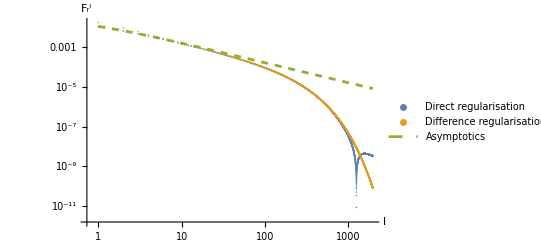

```mathematica
surfdiff = ListLogLogPlot[{Abs[smodesext6],Abs[sdiffmodes6],(Table[coeff[l, Z1, 0], {l,1,lm3}])}, AxesLabel->{"l", "F_r^l"}, Joined-> {False, False, True}, PlotStyle->{Thick,Thick, Dashed}, PlotLegends->Placed[{"Direct regularisation","Difference regularisation", "Asymptotics", FontSize-> 10}, {0.25,0.25}]]
```

```mathematica
Export["C:\\Users\\smp23ans\\Desktop\\Research\\Projects\\PhD\\Self Force Differences and Interior Schwarszchild\\Mathematica Code\\Modes data for Reg Plots\\smodesext6_Δr_0.005.mx", smodesext6];
```

```mathematica
Export["C:\\Users\\smp23ans\\Desktop\\Research\\Projects\\PhD\\Self Force Differences and Interior Schwarszchild\\Mathematica Code\\Modes data for Reg Plots\\sdiffmodes6_Δr_0.005.mx", sdiffmodes6];
```

```mathematica
Export["C:\\Users\\smp23ans\\Desktop\\Research\\Projects\\PhD\\Self Force Differences and Interior Schwarszchild\\Mathematica Code\\Reg Plots\\Comparing_asymptotics_vs_numerics.pdf", surfdiff];
```

```mathematica
Z1 = SetPrecision[2,WP];
xp1 = SetPrecision[2.5, WP];
xp2 = SetPrecision[2.25, WP];
xp3 = SetPrecision[2.1, WP];
xp4 = SetPrecision[2.05, WP];
xp5 = SetPrecision[2.025, WP];
xp6 = SetPrecision[2.005, WP];
```

#### Direct Method

```mathematica
(*This data generation takes some time*)
```

```mathematica
lm = 1000;
```

```mathematica
smodesext1 = Table[SetPrecision[SSRegFB[l,xp1,Z1], WP], {l,1,lm}];
```

```mathematica
smodesext2 = Table[SetPrecision[SSRegFB[l,xp2,Z1], WP], {l,1,lm}];
```

```mathematica
smodesext3 = Table[SetPrecision[SSRegFB[l,xp3,Z1], WP], {l,1,lm}];
```

```mathematica
smodesext4 = Table[SetPrecision[SSRegFB[l,xp4,Z1], WP], {l,1,lm}];
```

```mathematica
smodesext5 = Table[SetPrecision[SSRegFB[l,xp5,Z1], WP], {l,1,lm}];
```

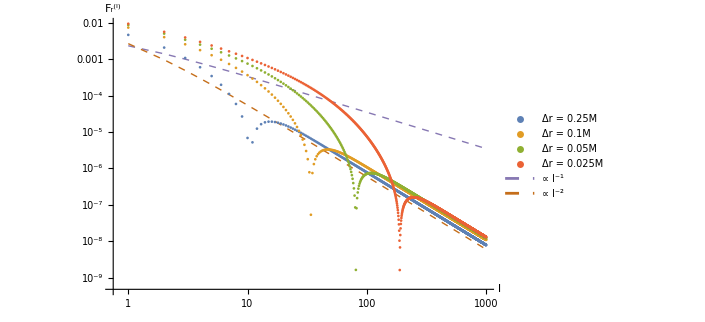

```mathematica
SurfForce = ListLogLogPlot[{ Abs[smodesext2],Abs[smodesext3], Abs[smodesext4], Abs[smodesext5],Table[3.5*10^-3(l+1/2)^-1, {l,1,lm}],Table[6*10^-3(l+1/2)^-2, {l,1,lm}]}, PlotLegends->Placed[{"Δr = 0.25M","Δr = 0.1M","Δr = 0.05M","Δr = 0.025M","∝ l^-1","∝ l^-2"}, Scaled[{0.19, 0.35}]],PlotStyle-> {(*Thick,*) Thick,Thick,Thick, Thick, {Dashed, Thin},  {Dashed, Thin}},Joined-> {(*False, *)False, False, False,False,True, True},AxesLabel->{"l", "F_r^(l)"}]
```

#### Difference Method and Asymptotics

```mathematica
lm2 = 30;
```

```mathematica
Subscript[Ω, s][Z_,ξ_]= Log[(ξ+√(ξ^2-1))/(Z+√(Z^2-1))];
diffscaling[Z_,ξ_] = (ξ+1)^(-3/2)/(4(Z+1)√(ξ-1));
```

```mathematica
sdiffmodes1 = Table[SetPrecision[Scadiff[l,xp1,Z1],WP], {l,1,lm2}];
```

```mathematica
sdiffmodes2 = Table[SetPrecision[Scadiff[l,xp4,Z1],WP], {l,1,lm2}];
```

```mathematica
sdiffmodes3 = Table[SetPrecision[Scadiff[l,xp5,Z1],WP], {l,1,lm2}];
```

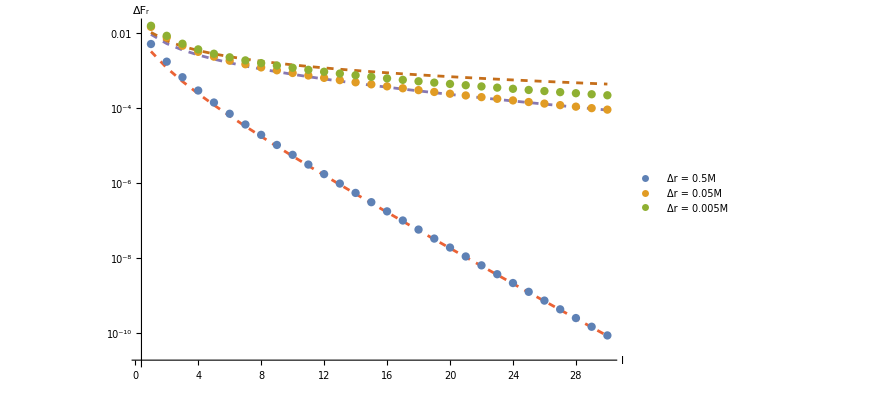

```mathematica
SurfSFdiff = ListLogPlot[{sdiffmodes1, sdiffmodes2, sdiffmodes3,  Table[diffscaling[Z1,xp1] ⅇ^(-Subscript[Ω, s][Z1,xp1](2l+1))/(l+1/2), {l,1,lm2}],Table[diffscaling[Z1,xp4] ⅇ^(-Subscript[Ω, s][Z1,xp4](2l+1))/(l+1/2), {l,1,lm2}],Table[diffscaling[Z1,xp6] ⅇ^(-Subscript[Ω, s][Z1,xp6](2l+1))/(l+1/2), {l,1,lm2}]},PlotLegends->Placed[{"Δr = 0.5M","Δr = 0.05M","Δr = 0.005M"},{0.19, 0.35}], PlotRange->All, PlotStyle-> {Thick, Thick,Thick,Dashed,Dashed, Dashed},Joined-> { False, False,False, True,True, True}, AxesLabel->{"l", "ΔF_r"}]
```

### Scalar Interior

#### Direct Method

```mathematica
lm5 = 300;
Z1 = SetPrecision[2, WPI];
xm1 = SetPrecision[1.5, WPI];
xm2 = SetPrecision[1.75, WPI];
xm3 = SetPrecision[1.9, WPI];
xm4 = SetPrecision[1.95, WPI];
xm5 = SetPrecision[1.975, WPI];
```

```mathematica
smodesint1 = Table[SetPrecision[zRegForce[l,xm1,Z1],WPI], {l,1,lm5}];
```

```mathematica
smodesint2 = Table[SetPrecision[zRegForce[l,xm2,Z1],WPI], {l,1,lm5}];
```

```mathematica
smodesint3 = Table[SetPrecision[zRegForce[l,xm3,Z1],WPI], {l,1,lm5}];
```

```mathematica
smodesint4 = Table[SetPrecision[zRegForce[l,xm4,Z1],WPI], {l,1,lm5}];
```

```mathematica
smodesint5 = Table[SetPrecision[zRegForce[l,xm5,Z1],WPI], {l,1,lm5}];
```

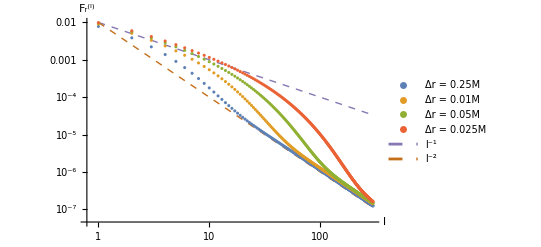

```mathematica
ListLogLogPlot[{Abs[smodesint2],Abs[smodesint3],Abs[smodesint4],Abs[smodesint5],Table[10^-2 l^-1, {l,1,lm5}],Table[10^-2 l^-2, {l,1,lm5}]}, PlotLegends->Placed[{"Δr = 0.25M","Δr = 0.01M","Δr = 0.05M","Δr = 0.025M","l^-1", "l^-2"}, Scaled[{0.175,0.375}]],PlotStyle-> {Thick, Thick,Thick, Thick,   {Dashed, Thin},  {Dashed, Thin}},Joined-> { False, False, False, False, True, True},AxesLabel->{"l", "F_r^(l)"}]
```

```mathematica
Export["C:\\Users\\smp23ans\\Desktop\\Research\\Projects\\PhD\\Self Force Differences and Interior Schwarszchild\\Mathematica Code\\Reg Plots\\IntSurface_force.pdf.pdf", IntSurfSF];
```

#### Difference Method

```mathematica
lm5 = 300;
Z1 = SetPrecision[2, WPI];
xm1 = SetPrecision[1.5, WPI];
xm2 = SetPrecision[1.75, WPI];
xm3 = SetPrecision[1.9, WPI];
xm4 = SetPrecision[1.95, WPI];
xm5 = SetPrecision[1.975, WPI];
```

```mathematica
sdiffmodesint1 = Table[SetPrecision[intdiff[l,xm1,Z1],WPI], {l,1,lm5}];
```

```mathematica
sdiffmodesint4 = Table[SetPrecision[intdiff[l,xm4,Z1],WPI], {l,1,lm5}];
```

```mathematica
sdiffmodesint5 = Table[SetPrecision[intdiff[l,xm5,Z1],WPI], {l,1,lm5}];
```

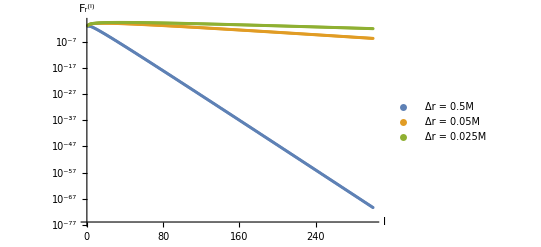

```mathematica
ListLogPlot[{Abs[sdiffmodesint1],Abs[sdiffmodesint4],Abs[sdiffmodesint5]}, PlotLegends->Placed[{"Δr = 0.5M","Δr = 0.05M","Δr = 0.025M"}, Scaled[{0.175,0.375}]],AxesLabel->{"l", "F_r^(l)"}]
```

### EM Exterior

#### Comparing asymptotics with exterior data

```mathematica
lm6=1000;
xp6=SetPrecision[2.005, WP];
Z6=SetPrecision[2, WP];
```

```mathematica
coeff[l_, Z_, δ_] =(q^2 (Z+√(-1+Z^2))^(2 l+1) (Z+δ+√(-1+(Z+δ)^2))^(-2 l-1))/(4 (l +1/2)M^2 (1+Z) √(-1+Z+δ) (1+Z+δ)^(3/2));
```

```mathematica
EMcoeff[l_, Z_, δ_] =3coeff[l,Z,δ];
```

```mathematica
EMmodesext6 = Table[SetPrecision[EMBareExtModes[l,xp6,Z6]+EMBz[xp6]+EMDz[xp6]/((l-1/2)(l+3/2)), WP], {l,1,lm6}];
```

```mathematica
emdiffmodesext6 = Table[SetPrecision[EMSFdiff[l,xp6,Z6], WP], {l,1,lm6}];
```

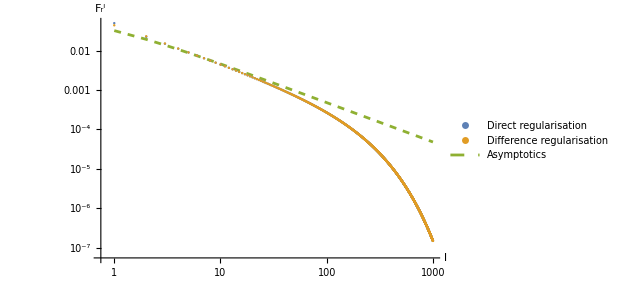

```mathematica
ListLogLogPlot[{Abs[EMmodesext6],Abs[emdiffmodesext6],(Table[EMcoeff[l, Z6, 0], {l,1,lm6}])}, AxesLabel->{"l", "F_r^l"}, Joined-> {False, False, True}, PlotStyle->{Thick,Thick, Dashed}, PlotLegends->Placed[{"Direct regularisation","Difference regularisation", "Asymptotics", FontSize-> 10}, {0.25,0.25}]]
```

#### Direct Method

```mathematica
(*This data generation takes some time*)
```

```mathematica
lm = 1000;
Z1 = SetPrecision[2,WP];
xp1 = SetPrecision[2.5, WP];
xp2 = SetPrecision[2.25, WP];
xp3 = SetPrecision[2.1, WP];
xp4 = SetPrecision[2.05, WP];
xp5 = SetPrecision[2.025, WP];
xp6 = SetPrecision[2.005, WP];
```

```mathematica
EMmodesext1 = Table[SetPrecision[EMBareExtModes[l,xp1,Z1]+EMBz[xp1], WP], {l,1,lm}];
```

```mathematica
EMmodesext2 = Table[SetPrecision[EMBareExtModes[l,xp2,Z1]+EMBz[xp2], WP], {l,1,lm}];
```

```mathematica
EMmodesext3 = Table[SetPrecision[EMBareExtModes[l,xp3,Z1]+EMBz[xp3], WP], {l,1,lm}];
```

```mathematica
EMmodesext4 = Table[SetPrecision[EMBareExtModes[l,xp4,Z1]+EMBz[xp4], WP], {l,1,lm}];
```

```mathematica
EMmodesext5 = Table[SetPrecision[EMBareExtModes[l,xp5,Z1]+EMBz[xp5], WP], {l,1,lm}];
```

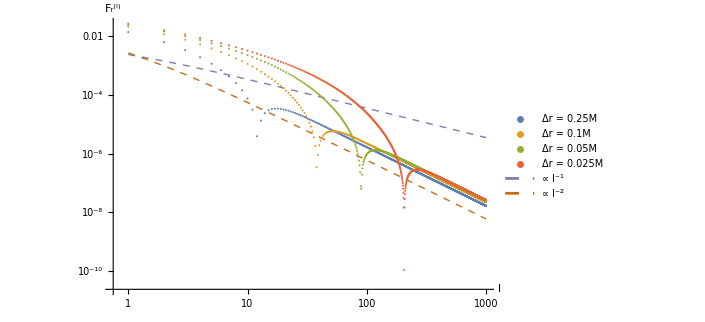

```mathematica
SurfForce = ListLogLogPlot[{ Abs[EMmodesext2],Abs[EMmodesext3], Abs[EMmodesext4], Abs[EMmodesext5],Table[3.5*10^-3(l+1/2)^-1, {l,1,lm}],Table[6*10^-3(l+1/2)^-2, {l,1,lm}]}, PlotLegends->Placed[{"Δr = 0.25M","Δr = 0.1M","Δr = 0.05M","Δr = 0.025M","∝ l^-1","∝ l^-2"}, Scaled[{0.19, 0.35}]],PlotStyle-> {Thick,Thick,Thick, Thick, {Dashed, Thin},  {Dashed, Thin}},Joined-> {False, False, False,False,True, True},AxesLabel->{"l", "F_r^(l)"}]
```

#### Difference Method & Asymptotics

```mathematica
Ωem[Z_,ξ_]= Log[(ξ+√(ξ^2-1))/(Z+√(Z^2-1))];
EMdiffscaling[Z_,ξ_] = (3(ξ+1)^(-3/2))/(4(Z+1)√(ξ-1));
coeff[l_, Z_, δ_] =(q^2 (Z+√(-1+Z^2))^(2 l+1) (Z+δ+√(-1+(Z+δ)^2))^(-2 l-1))/(4 (l +1/2)M^2 (1+Z) √(-1+Z+δ) (1+Z+δ)^(3/2));
EMcoeff[l_, Z_, δ_] =3coeff[l,Z,δ];
lm2=30;
Z0=2;
xp1 = SetPrecision[2.5, WP];
xp2 = SetPrecision[2.25, WP];
xp3 = SetPrecision[2.1, WP];
xp4 = SetPrecision[2.05, WP];
xp5 = SetPrecision[2.025, WP];
xp6 = SetPrecision[2.005, WP];
```

```mathematica
EMdiffmodes1 = Table[SetPrecision[EMSFdiff[l,xp1,Z0],WP], {l,1,lm2}];
```

```mathematica
EMdiffmodes2 = Table[SetPrecision[EMSFdiff[l,xp2,Z0],WP], {l,1,lm2}];
```

```mathematica
EMdiffmodes3 = Table[SetPrecision[EMSFdiff[l,xp3,Z0],WP], {l,1,lm2}];
```

```mathematica
EMdiffmodes4 = Table[SetPrecision[EMSFdiff[l,xp4,Z0],WP], {l,1,lm2}];
```

```mathematica
EMdiffmodes5 = Table[SetPrecision[EMSFdiff[l,xp5,Z0],WP], {l,1,lm2}];
```

```mathematica
EMdiffmodes6 = Table[SetPrecision[EMSFdiff[l,xp6,Z0],WP], {l,1,lm2}];
```

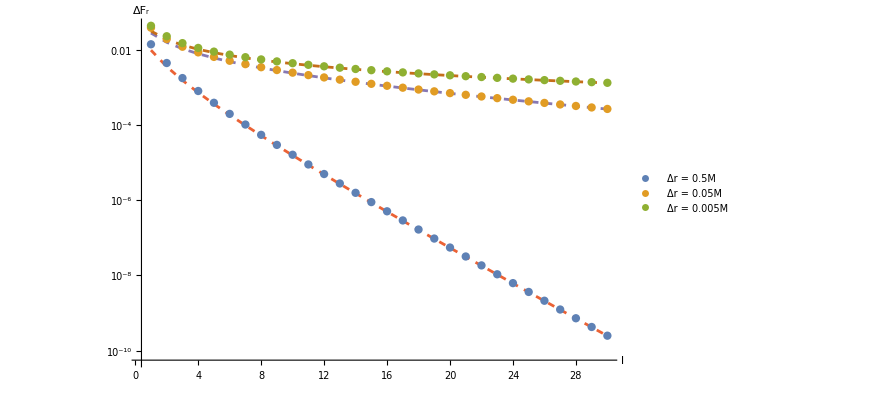

```mathematica
ListLogPlot[{EMdiffmodes1, EMdiffmodes4,  EMdiffmodes6,  Table[EMdiffscaling[Z0,xp1] ⅇ^(-Ωem[Z0,xp1](2l+1))/(l+1/2), {l,1,lm2}],Table[EMdiffscaling[Z0,xp4] ⅇ^(-Ωem[Z0,xp4](2l+1))/(l+1/2), {l,1,lm2}],Table[EMdiffscaling[Z0,xp6] ⅇ^(-Ωem[Z0,xp6](2l+1))/(l+1/2), {l,1,lm2}]},PlotLegends->Placed[{"Δr = 0.5M","Δr = 0.05M","Δr = 0.005M"},{0.19, 0.35}], PlotRange->All, PlotStyle-> {Thick, Thick,Thick, {Dashed},Dashed, { Dashed}},Joined-> { False, False,False, True,True, True}, AxesLabel->{"l", "ΔF_r"}]
```

## Data Tables

### Scalar Exterior

```mathematica
tablervals = {6.1, 6.5, 7, 8, 10, 15, 25};
Extscalardata = Table[{ScientificForm[ExtStarDirReg[6-1,ri-1][[1;;2]],12],ScientificForm[ExtStarDiffReg[6-1,ri-1][[1;;2]],12]}, {ri,tablervals}];
```

```mathematica
Extscalardata[[7]]
```

{{1.68634049176×10^-5+(0.×10^-79) ⅈ,1.68634049177×10^-5+(0.×10^-79) ⅈ},{1.68634049176×10^-5+(0.×10^-79) ⅈ,1.68634049176×10^-5+(0.×10^-79) ⅈ}}

### Scalar Interior

```mathematica
tablerintvals = {0.5, 1, 2, 3, 5, 5.9};
Intscalardata = Table[{ScientificForm[IntStarDirReg[6-1,ri-1, 2000][[{1,4}]],12],ScientificForm[IntStarDiffReg[6-1,ri-1, 50][[{1,2}]],12]}, {ri,tablerintvals}];
```

```mathematica
Intscalardata[[6,1]][[1,1]]
DecimalForm[Intscalardata[[6,1]][[1,2]]]
```

0.00548222013884459645087595888423610897402277680694189422584209855962298287105+0. ⅈ

0.000000000801849549219781779120498933912742148266694641733920434489846229553222656250

### EM Exterior

```mathematica
tablervals = {6.1, 6.5, 7, 8, 10, 15, 25};
ExtEMdata = Table[{ScientificForm[EMExtStarDirReg[6-1,ri-1][[1;;2]],12],ScientificForm[EMExtStarDiffReg[6-1,ri-1][[1;;2]]+EMExtStarDiffReg[6-1,ri-1][[4]],12]}, {ri,tablervals}];
```

```mathematica
ExtEMdata[[7]]
```

{{6.81037257301×10^-5+(0.×10^-79) ⅈ,6.81037257303×10^-5+(0.×10^-81) ⅈ},{6.81037257301×10^-5+(0.×10^-81) ⅈ,6.81037257301×10^-5+(0.×10^-81) ⅈ}}

### EM Interior

```mathematica
tablerintvals = {0.5, 1, 2, 3, 5, 5.9};
IntEMdata = Table[Print[StringForm["Evaluating r = ``", ri]]{ScientificForm[EMIntStarDirReg[6-1,ri-1,3000][[{1,2,4}]],12],ScientificForm[EMIntStarDiffReg[6-1,ri-1, 50][[1;;2]],12]}, {ri,tablerintvals}];
```

Evaluating r = 0.5

```mathematica
IntEMdata[[5]]
```

{{7.64248765998×10^-3+(0.×10^-77) ⅈ,7.64248761437×10^-3+(0.×10^-74) ⅈ,4.56124189019×10^-14},{7.64248884062×10^-3+(0.×10^-77) ⅈ,7.64248884062×10^-3+(0.×10^-277) ⅈ}}

```mathematica
t0=EMIntStarDirReg[6-1,0.5-1,1500];
```

```mathematica
t1=EMIntStarDiffReg[6-1,0.5-1];
```

```mathematica
t1[[1]]
t0[[1]]
t0[[2]]
t0[[4]]*10//DecimalForm
```

0.000518072685547250723327891514738088715173387279080903327009706224211247855243+0. ⅈ

0.000518072685540658209459883495040060783899394291001695548191350577753110761335+0. ⅈ

0.00051807268554048116178357509558863089025878653030252015326563447858174+0. ⅈ

0.00000000000000000177047676308399451521333602164352693852715220809273524368854246802129637217

```mathematica
t01=EMIntStarDirReg[6-1,5-1,1500];
```

```mathematica
t11=EMIntStarDiffReg[6-1,5-1,500];
```

```mathematica
t11[[1]]
t01[[1]]
t01[[4]]//DecimalForm
```

0.00764248884061927244844062924174349653695870692372759919662516161803548736888+0. ⅈ

0.0076424888571160454276461169505583991396547392901238104422773605185488005053+0. ⅈ

0.0000000000000000142854720396823857536417378075440874155578761323581379882874387021729489788

## Force over the full domain

### Scalar Self-Force

```mathematica
ScalarSuperSum[R_] :=  Module[{rvals,extr,intr,ffr,intresults,extresults,intdirectforce,intdiffforce,extdirectforce,extdiffforce,farfield,approxforce, ξ,Z,σ0,σ1,σ2,centre,centralapprox, surf, intlmaxresults,intsurf,intmag,extmag,farfieldmag,approxforcemag,centralapproxmag,intdiffforcemag},
rvals = Join[Subdivide[0.0005,R-1, 15],Subdivide[R-0.99, R-0.05, 10],Subdivide[R+0.05,R+0.99 ,10],Subdivide[R+1,10 ,30]];
(*rvals = Join[Subdivide[0.0005,R-1, 5],Subdivide[R-0.99, R-0.05, 5],Subdivide[R+0.05,R+0.99 ,2],Subdivide[R+1,10 ,5]];*)
extr = Select[rvals, R<#&];
intr = Select[rvals, 0<#<R&];
intsurf = Select[rvals, R-1<#<R&];
centre = Select[rvals, 0.0005<=#<1.5&];
ffr = Select[rvals, R+3<#<=10&];
surf=Select[rvals, R<#<R+0.5&];
(*Data Generation for Numerical Sum*)
intresults=Table[Print[StringForm["For r0 value `1`, generating data", r0]];
{IntStarDirReg[R-1,r0-1,250],IntStarDiffReg[R-1,r0-1]}, {r0,intr}];
extresults=Table[Print[StringForm["For r0 value `1`, generating data", r0]];
{ExtStarDirReg[R-1,r0-1,250],ExtStarDiffReg[R-1,r0-1]}, {r0,extr}];
intlmaxresults=Transpose[{intresults[[All,1,3]],intresults[[All,2,3]]}];
intdirectforce=Table[{intr[[j]],intresults[[j,1,1]]},{j,1,Length[intr]}];
intdiffforce=Table[{intr[[j]],intresults[[j,2,1]]},{j,1,Length[intr]}];
extdirectforce=Table[{extr[[j]],extresults[[j,1,1]]},{j,1,Length[extr]}];
extdiffforce=Table[{extr[[j]],extresults[[j,2,1]]},{j,1,Length[extr]}];
(*Force Magnitudes*)
intdiffforcemag=Table[{intr[[j]],intresults[[j,2,1]] √(1-2M intr[[j]]^2/R^3)},{j,1,Length[intr]}];
intmag=Table[{intr[[j]], SetPrecision[intdiffforce[[j,2]] √(1-2M intr[[j]]^2/R^3),WP]}, {j,1,Length[intr]}]; 
extmag=Table[{extr[[j]], SetPrecision[extdiffforce[[j,2]] √(1-(2M)/extr[[j]]),WP]}, {j,1,Length[extr]}]; 
(*Exterior FarField Approximation*)
farfield = Table[{r0,SetPrecision[(1/r0^3 +2 1/r0^4+23/6 1/r0^5) SLZ[0,R-1],WP]},{r0,ffr}]; 
farfieldmag = Table[{r0,SetPrecision[((1/r0^3 +2 1/r0^4+23/6 1/r0^5) SLZ[0,R-1])√(1-(2M)/r0),WP]},{r0,ffr}]; 
(*Exterior Surface Approximation*)
   approxforce = Table[{r0, SetPrecision[1/(4 (1+Z) √(ξ-1) (ξ+1)^(3/2))Log[Coth[1/2 Log[(ξ+√(ξ^2-1))/(Z+√(Z^2-1))]]],WP]/.{Z-> R-1, ξ-> r0-1}},{r0,surf}];
approxforcemag = Table[{r0, SetPrecision[(1/(4 (1+Z) √(ξ-1) (ξ+1)^(3/2))Log[Coth[1/2 Log[(ξ+√(ξ^2-1))/(Z+√(Z^2-1))]]])√(1-(2M)/r0),WP]/.{Z-> R-1, ξ-> r0-1}},{r0,surf}];
(*Central Approximation*)
σ0 =1-(56372536560134831 M^10)/(23216016221798400 R^10)-(335232256205723 M^9)/(145100101386240 R^9)-(86825071649491 M^8)/(51821464780800 R^8)-(32572120766989 M^7)/(51011754393600 R^7)-(37277896721 M^6)/(108999475200 R^6)-(32449741 M^5)/(61931520 R^5)+(41424469 M^4)/(30965760 R^4)-(298 M^3)/(45 R^3)-(31 M^2)/(12 R^2)-(4 M)/(3 R);
σ1 = 1+(349804504538535351315034873 M^13)/(21823798161009593548800000 R^13)+(62968827000049022217171287 M^12)/(3819164678176678871040000 R^12)+(101227057397656868068757 M^11)/(7749928324222156800000 R^11)+(712385464906290882754517 M^10)/(74593060120638259200000 R^10)+(32338648671111278338489 M^9)/(4662066257539891200000 R^9)+(29334750330926323560763 M^8)/(5244824539732377600000 R^8)+(2781740752432777951 M^7)/(803435131699200000 R^7)+(621906550507105511 M^6)/(13390585528320000 R^6)+(533398271 M^5)/(10692000 R^5)+(6125213 M^4)/(283500 R^4)+(89099 M^3)/(9450 R^3)+(151 M^2)/(36 R^2)+(79 M)/(30 R);
σ2= 1-(2052654795078215338165808029427467 M^11)/(1752193246117819003699200000000000 R^11)-(1696842285459865908158144508035513 M^10)/(3022533349553237781381120000000000 R^10)-(117629838894726992920818689 M^9)/(447556398574731264000000000 R^9)-(856203762783214812853701 M^8)/(7163270400468582400000000 R^8)-(5725942715428638323 M^7)/(107106315796480000000 R^7)-(5337948827405143 M^6)/(202511941632000000 R^6)-(121084408719 M^5)/(5740134400000 R^5)-(2780229721 M^4)/(77271040000 R^4)-(882841 M^3)/(18816000 R^3)-(109251 M^2)/(22400 R^2)-(2553 M)/(280 R);
centralapprox = Table[{r0, SetPrecision[(q^2 M)/3 r0/R^4(σ1 -M/R σ0+ r0^2(2/(5 R^2)σ2+M/R^3(29/10 σ1+3/4 σ2)+M^2/R^4(123/64 σ2+45/16 σ1-46/15 σ0))),WP]},{r0,centre}]; 
centralapproxmag = Table[{r0, SetPrecision[((q^2 M)/3 r0/R^4(σ1 -M/R σ0+ r0^2(2/(5 R^2)σ2+M/R^3(29/10 σ1+3/4 σ2)+M^2/R^4(123/64 σ2+45/16 σ1-46/15 σ0))))√(1-2M r0^2/R^3),WP]},{r0,centre}]; 
{intdirectforce,intdiffforce,centralapprox,extdirectforce,extdiffforce,approxforce,farfield,rvals,intlmaxresults, intmag, extmag,farfieldmag,approxforcemag,centralapproxmag,intdiffforcemag}
]
```

```mathematica
SR4Full=ScalarSuperSum[4];
```

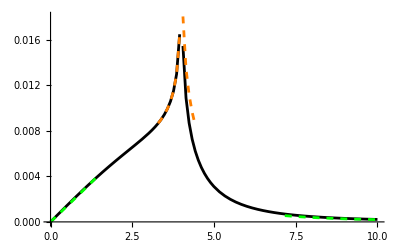

```mathematica
ListPlot[{Re@SR4Full[[10]],Re@SR4Full[[11]],Re@SR4Full[[-1]][[Round[0.75*Length[SR4Full[[-1]]]];;]],Re@SR4Full[[13]],Re@SR4Full[[12]], Re@SR4Full[[-2]]}, PlotRange->All, Joined->True, PlotStyle->{Black, Black,{Orange, Dashed}, {Orange, Dashed}, {Green, Dashed},{Green, Dashed}}]
```

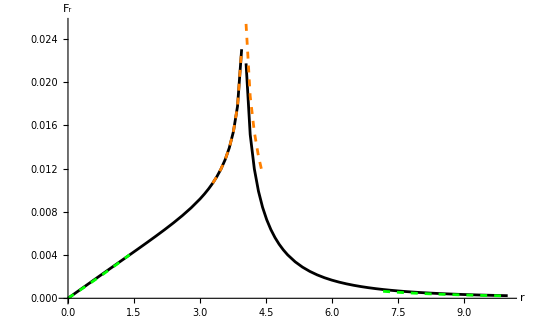

```mathematica
Scalarfullplot=ListPlot[{Re@SR4Full[[1]],Re@SR4Full[[4]],Re@SR4Full[[2]][[Round[0.75*Length[SR4Full[[2]]]];;]],Re@SR4Full[[6]],Re@SR4Full[[7]], Re@SR4Full[[3]]}, PlotRange->All, Joined->True, PlotStyle->{Black, Black,{Orange, Dashed}, {Orange, Dashed}, {Green, Dashed},{Green, Dashed}}, AxesLabel->{Style["r",14], Style["F_r",14]}]
```

```mathematica
SR4Full=Import["C:\\Users\\smp23ans\\Desktop\\Research\\Projects\\PhD\\Self Force Differences and Interior Schwarszchild\\Self Force and the Schwarzschild Star - Paper Files\\Data\\Full Domain Plots\\ScalarData_R4.mx"];
```

```mathematica
SR6Full=ScalarSuperSum[6];
```

For r0 value 0.0005, generating data

For r0 value 0.3338, generating data

For r0 value 0.6671, generating data

For r0 value 1.0004, generating data

$Aborted

```mathematica
SR8Full=ScalarSuperSum[8];
```

```mathematica
Export["C:\\Users\\smp23ans\\Desktop\\Research\\Projects\\PhD\\Self Force Differences and Interior Schwarszchild\\Self Force and the Schwarzschild Star - Paper Files\\Plots\\Scalarfullplot.pdf", Scalarfullplot]
```

C:\Users\smp23ans\Desktop\Research\Projects\PhD\Self Force Differences and Interior Schwarszchild\Self Force and the Schwarzschild Star - Paper Files\Plots\Scalarfullplot.pdf

### EM Self-Force

```mathematica
EMSuperSum[R_] :=  Module[{rvals,extr,intsurf,intr,centre,surf,ffr,intresults,extresults,intlmaxresults,intdirectforce,intdiffforce,extdirectforce,extdiffforce,EMfarfield,EMapproxforce, ξ,Z,Γ1,Γ2,EMcentralapprox,intdiffforcemag,intmag,extmag,EMfarfieldmag,EMapproxforcemag,EMcentralapproxmag},
rvals = Join[Subdivide[0.0005,R-1, 15],Subdivide[R-0.99, R-0.05, 10],Subdivide[R+0.05,R+0.99 ,10],Subdivide[R+1,10 ,30]];
(*rvals = Join[Subdivide[0.0005,R-1, 5],Subdivide[R-0.99, R-0.05, 5],Subdivide[R+0.05,R+0.99 ,2],Subdivide[R+1,10 ,5]];*)
extr = Select[rvals, R<#&];
intr = Select[rvals, 0<#<R&];
intsurf = Select[rvals, R-1<#<R&];
centre = Select[rvals, 0.0005<=#<1.5&];
ffr = Select[rvals, R+3<#<=10&];
surf=Select[rvals, R<#<R+1&];
(*Data Generation for Numerical Sum*)
intresults=Table[Print[StringForm["For r0 value `1`, generating data", r0]];
{EMIntStarDirReg[R-1,r0-1,250],EMIntStarDiffReg[R-1,r0-1]}, {r0,intr}];
extresults=Table[Print[StringForm["For r0 value `1`, generating data", r0]];
{EMExtStarDirReg[R-1,r0-1,250],EMExtStarDiffReg[R-1,r0-1]}, {r0,extr}];
intlmaxresults=Transpose[{intresults[[All,1,3]],intresults[[All,2,3]]}];
intdirectforce=Table[{intr[[j]],intresults[[j,1,1]]},{j,1,Length[intr]}];
intdiffforce=Table[{intr[[j]],intresults[[j,2,1]]},{j,1,Length[intr]}];
extdirectforce=Table[{extr[[j]],extresults[[j,1,1]]},{j,1,Length[extr]}];
extdiffforce=Table[{extr[[j]],extresults[[j,2,1]]},{j,1,Length[extr]}];
(*Force Magnitudes*)
intdiffforcemag=Table[{intr[[j]],intresults[[j,2,1]] √(1-2M intr[[j]]^2/R^3)},{j,1,Length[intr]}];
intmag=Table[{intr[[j]], SetPrecision[intdiffforce[[j,2]] √(1-2M intr[[j]]^2/R^3),WP]}, {j,1,Length[intr]}]; 
extmag=Table[{extr[[j]], SetPrecision[extdiffforce[[j,2]] √(1-(2M)/extr[[j]]),WP]}, {j,1,Length[extr]}]; 
(*Exterior FarField Approximation*)
EMfarfield = Table[{r0,SetPrecision[2/5 q^2 M R^2/r0^5( (1+(7M)/(2r0) + 91/10 (M/r0)^2 ) EMSlz[1,R/M-1]/((3 R^2)/(10 M^5))ν[1,M]/κ[1,M] + 9/14(R/r0)^2 EMSlz[2,R/M-1]/((9 R^4)/(14 M^9))ν[2,M]/κ[2,M])+(q^2 M)/r0^3(1-2 M/r0)^(-1/2),WP]},{r0,ffr}];  
EMfarfieldmag = Table[{r0,SetPrecision[(2/5 q^2 M R^2/r0^5( (1+(7M)/(2r0) + 91/10 (M/r0)^2 ) EMSlz[1,R/M-1]/((3 R^2)/(10 M^5))ν[1,M]/κ[1,M] + 9/14(R/r0)^2 EMSlz[2,R/M-1]/((9 R^4)/(14 M^9))ν[2,M]/κ[2,M])+(q^2 M)/r0^3(1-2 M/r0)^(-1/2))√(1-(2M)/r0),WP]},{r0,ffr}]; 
(*Approximation in the Exterior*)
EMapproxforce = Table[{r0, SetPrecision[(-3 (Z+√(-1+Z^2))+3 (ξ+√((ξ-1) (1+ξ))) ArcTanh[(Z+√(-1+Z^2))/(ξ+√(-1+(ξ)^2))])/(2 (1+Z) √(ξ-1) (1+ξ)^(3/2) (ξ+√(-1+(ξ)^2)))+ BHf[ξ],WP]/.{Z-> R-1, ξ-> r0-1}},{r0,surf}];  
EMapproxforcemag = Table[{r0, SetPrecision[((-3 (Z+√(-1+Z^2))+3 (ξ+√((ξ-1) (1+ξ))) ArcTanh[(Z+√(-1+Z^2))/(ξ+√(-1+(ξ)^2))])/(2 (1+Z) √(ξ-1) (1+ξ)^(3/2) (ξ+√(-1+(ξ)^2)))+ BHf[ξ])√(1-(2M)/r0),WP]/.{Z-> R-1, ξ-> r0-1}},{r0,surf}];
(*Central Approximation*)
Γ1=1+(110871593939409 M^10)/(18897856102400 R^10)+(127980385006041 M^9)/(20669530112000 R^9)+(55403527475889 M^8)/(10334765056000 R^8)+(51244130481 M^7)/(10092544000 R^7)+(30003346719 M^6)/(4037017600 R^6)+(4374767 M^5)/(132000 R^5)+(75193 M^4)/(5250 R^4)+(1089 M^3)/(175 R^3)+(11 M^2)/(4 R^2)+(13 M)/(10 R);
Γ2= 1+(6183668530339297 M^6)/(22501326848000000 R^6)+(8304631998519 M^5)/(40180940800000 R^5)+(11981145639 M^4)/(77271040000 R^4)+(1675847 M^3)/(18816000 R^3)-(5379 M^2)/(22400 R^2)-(1881 M)/(280 R);
EMcentralapprox = Table[{r0, SetPrecision[ q^2(M r0)/R^4(Γ1 + r0^2/R^2(2/5 Γ2+M/R(23/10 Γ1+3/4 Γ2)+M^2/R^2(123/64 Γ2+39/16 Γ1))),WP]},{r0,centre}];  
EMcentralapproxmag = Table[{r0, SetPrecision[(q^2(M r0)/R^4(Γ1 + r0^2/R^2(2/5 Γ2+M/R(23/10 Γ1+3/4 Γ2)+M^2/R^2(123/64 Γ2+39/16 Γ1))))√(1-2M r0^2/R^3),WP]},{r0,centre}]; 
{intdirectforce,intdiffforce,EMcentralapprox,extdirectforce,extdiffforce,EMapproxforce,EMfarfield,rvals,intlmaxresults,intdiffforcemag,intmag,extmag,EMfarfieldmag,EMapproxforcemag,EMcentralapproxmag}
]
```

```mathematica
EMR4Full=EMSuperSum[4];
```

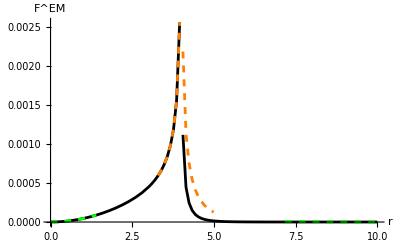

```mathematica
ListPlot[{Re@EMR4Full[[11]],Re@EMR4Full[[12]],Re@EMR4Full[[10]][[Round[0.75*Length[EMR4Full[[10]]]];;]],Re@EMR4Full[[14]],Re@EMR4Full[[13]], Re@EMR4Full[[15]]}, PlotRange->All, Joined->True, PlotStyle->{Black, Black,{Orange, Dashed}, {Orange, Dashed}, {Green, Dashed},{Green, Dashed}}, AxesLabel->{"r","F^EM"}]
```

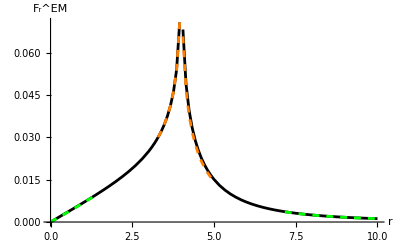

```mathematica
EMfullplot=ListPlot[{Re@EMR4Full[[1]],Re@EMR4Full[[4]],Re@EMR4Full[[2]][[Round[0.75*Length[EMR4Full[[2]]]];;]],Re@EMR4Full[[6]],Re@EMR4Full[[7]], Re@EMR4Full[[3]]}, PlotRange->All, Joined->True, PlotStyle->{Black, Black,{Orange, Dashed}, {Orange, Dashed}, {Green, Dashed},{Green, Dashed}}, AxesLabel->{Style["r",14], Style["F_r^EM",14]}]
```

```mathematica
Export["C:\\Users\\smp23ans\\Desktop\\Research\\Projects\\PhD\\Self Force Differences and Interior Schwarszchild\\Self Force and the Schwarzschild Star - Paper Files\\Plots\\EMfullplot.pdf", EMfullplot]
```

C:\Users\smp23ans\Desktop\Research\Projects\PhD\Self Force Differences and Interior Schwarszchild\Self Force and the Schwarzschild Star - Paper Files\Plots\EMfullplot.pdf

```mathematica
Export["C:\\Users\\smp23ans\\Desktop\\Research\\Projects\\PhD\\Self Force Differences and Interior Schwarszchild\\Self Force and the Schwarzschild Star - Paper Files\\Data\\Full Domain Plots\\EMData_R4.mx",EMR4Full];
```

### Log-Linear Plot

```mathematica
ScalarExtSum[R_] :=  Module[{ϵvals,rvals,extresults,extdirectforce,extdiffforce,approxforce, ξ,Z},
ϵvals = Subdivide[SetPrecision[0.25, WP],SetPrecision[0.01, WP], 15];
(*ϵvals = Subdivide[SetPrecision[0.25, WP],SetPrecision[0.1, WP], 3];*)
rvals = ϵvals + R;
(*Data Generation for Numerical Sum*)
extresults=Table[Print[StringForm["For r0 value `1`, generating data", r0]];
{ExtStarDirReg[R-1,r0-1,250],ExtStarDiffReg[R-1,r0-1]}, {r0,rvals}];
extdirectforce=Table[{rvals[[j]],extresults[[j,1,1]]},{j,1,Length[rvals]}];
extdiffforce=Table[{ϵvals[[j]],extresults[[j,2,1]]},{j,1,Length[rvals]}];
(*Exterior Surface Approximation*)
   approxforce = Table[{ϵvals[[j]], SetPrecision[1/(4 (1+Z) √(ξ-1) (ξ+1)^(3/2))Log[Coth[1/2 Log[(ξ+√(ξ^2-1))/(Z+√(Z^2-1))]]],WP]/.{Z-> R-1, ξ-> rvals[[j]]-1}},{j,1,Length[rvals]}];
{extdirectforce,extdiffforce,approxforce}
]
```

```mathematica
EMExtSum[R_] :=  Module[{ϵvals,rvals,extresults,extdirectforce,extdiffforce,EMapproxforce, ξ,Z},
ϵvals = Subdivide[SetPrecision[0.25, WP],SetPrecision[0.01, WP], 15];
(*ϵvals = Subdivide[SetPrecision[0.25, WP],SetPrecision[0.1, WP], 3];*)
rvals = ϵvals + R;
(*Data Generation for Numerical Sum*)
extresults=Table[Print[StringForm["For r0 value `1`, generating data", r0]];
{EMExtStarDirReg[R-1,r0-1,250],EMExtStarDiffReg[R-1,r0-1]}, {r0,rvals}];
extdirectforce=Table[{ϵvals[[j]],extresults[[j,1,1]]},{j,1,Length[rvals]}];
extdiffforce=Table[{rvals[[j]],extresults[[j,2,1]]},{j,1,Length[rvals]}];
(*Approximation in the Exterior*)
EMapproxforce = Table[{ϵvals[[j]], SetPrecision[(-3 (Z+√(-1+Z^2))+3 (ξ+√((ξ-1) (1+ξ))) ArcTanh[(Z+√(-1+Z^2))/(ξ+√(-1+(ξ)^2))])/(2 (1+Z) √(ξ-1) (1+ξ)^(3/2) (ξ+√(-1+(ξ)^2)))+ BHf[ξ],WP]/.{Z-> R-1, ξ-> rvals[[j]]-1}},{j,1,Length[rvals]}];  
{extdirectforce,extdiffforce,EMapproxforce,rvals}
]
```

```mathematica
LLScalar=ScalarExtSum[4];
```

```mathematica
LLEM=EMExtSum[4];
```

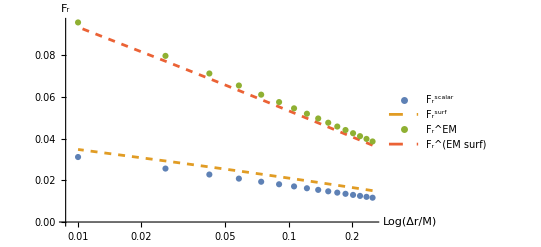

```mathematica
LLplots = ListLogLinearPlot[{LLScalar[[2]],LLScalar[[3]],LLEM[[1]],LLEM[[3]]}, Joined->{False, True, False, True}, AxesLabel->{Style["Log(Δr/M)",14], Style["F_r",14]}, PlotLegends->{Style["F_r^scalar",14], Style["F_r^surf",14], Style["F_r^EM",14], Style["F_r^(EM surf)",14]}, PlotStyle->{Thick, Dashed, Thick, Dashed}]
```

```mathematica
Export["C:\\Users\\smp23ans\\Desktop\\Research\\Projects\\PhD\\Self Force Differences and Interior Schwarszchild\\Self Force and the Schwarzschild Star - Paper Files\\Plots\\log_linear_plots.pdf", LLplots]
```

C:\Users\smp23ans\Desktop\Research\Projects\PhD\Self Force Differences and Interior Schwarszchild\Self Force and the Schwarzschild Star - Paper Files\Plots\log_linear_plots.pdf